# Polish Prefix Grammars, Type Systems, and Algebra Travesties —- Revision 9

## Brian Beckman 14 June 2012; 23 Sept 2021; Dec 2023

## OVERVIEW

Mathematica supports an extremely easy and straightforward way to generate parsers and other syntax-directed tools like test generators for languages in Polish Prefix Form (PPF). In (our version of) this form, each term in the grammar has a unique leading head symbol. Arities of functional forms are fixed. Punctuation is not needed because the head immediately dictates how many tokens to consume for arguments For example, f x y z is f[x, y, z] transcribed to our punctuation-free PPF. The head is f, a non-terminal in the grammar. The expansion of f in the grammar specifies that f require three arguments, x, y, and z. These are meta-syntactic variables, standing for arbitrary utterances in the grammar, not for specific terms.

The following are easy in PPF: parsing and parser generation (utterances to trees), antiparsing (travesties: random, syntactically valid utterances) unparsing (trees to utterances). We illustrate using the famous game “Wff-n-Proof” as a motivating example. Then we move on to algebra formulas and type systems, a-la Benjamin C. Pierce, via PPF grammars.

Any language that can be transcribed into PPF can enjoy the techniques presented in this paper. We promote the idea that it might be worth the effort to transcribe some complicated syntax like C++, Python, or Haskell, into PPF to ease the work of downstream language-processing tools like parsers and test generators.

(Physical copies of Wff-n-Proof are not difficult to find on-line. My old URLs to digital versions are now dead.)

### Preliminaries

## PRELIMINARY PACKAGES

```mathematica
<<Utilities`CleanSlate`
```

If you like, move the following packages onto your Mathematica $Path. The following unevaluatable cell shows where I put them on my system. I include copies of these packages here so anyone can just evaluate this notebook without installing packages. We don’t explain this code, here, we just use it. Close up this chapter so you don’t have to look at all this stuff.

```mathematica
<<"~/Dropbox/MMA/Packages/JacquardProlog.m"
<<"~/Dropbox/MMA/logic.m"
<<"~/Dropbox/MMA/Packages/Jacquard.m"
```

## logic.m

```mathematica
(* :Context: logic` *)

(* :Title: Logic Programming *)

(* :Author: Lic. Renán Cabrera *)

(* :Summary: This is package for Logic Programming 
    Tested under Mathematica 3.0 
*)
```

```mathematica
(* :Package Version: 1.0       December 2000 *)

(*  Mathematica is a registered trademark of Wolfram Research, Inc.   *)

BeginPackage[ "logic`" ]
```

logic`

```mathematica
Question::usage     = "Question[ Statements, Query, Var]" 
AddKnowledge::usage = "AddKnowledge[ Statements, Rule ]"
```

Question[ Statements, Query, Var]

AddKnowledge[ Statements, Rule ]

```mathematica
Begin["`Private`"]
```

logic`Private`

Question first makes a fresh variable in the Module expression. The superficial name of the fresh variable is Answer, but, internally, Mathematica makes session-fresh name of the form $479 that is guaranteed not to collide with any other variable in this session.

The first argument of the Cases expression is a ReplaceRepeated expression (the original was "ReplaceAll," but it did not yield sufficient results). It searches the given knowledge base for all terms matching the pattern and rewrites them to Answer[X], where X is the declared variable provided by the user in the third parameter position of the Question expression. This is the input list that Cases will search. Cases then searches the resulting list for terms matching Answer[_], that is, Answer[anything], and rewrites the Answers to Sequences, stripping off the placeholder name Answer, so that the final results just appear in list form.

```mathematica
Question[Knowledge_, Patt_ , X_ ] :=
  Module[ {Answer}, 
    Cases[Knowledge //. Patt -> Answer[X],
	  Answer[_]] /. Answer -> Sequence ];
```

The second form of Question just yields "True" or "False." Cabrera's original (commented out) was not able to recognize questions of the form Question[Knowledge, Statements[ . . . ]], but the following will do.

```mathematica
Question[Knowledge_, Patt_] :=
  Question[Knowledge, Patt, Unique[]] =!= {};
  (*Cases[Knowledge, Patt ] =!= {};*)
```

This implementation of AddKnowledge just brute-forces all implications of the rules into the factbase. This is not scaleable. UNDONE: fix

```mathematica
AddKnowledge[K_, R_]:= Union[K, K //. R];
```

```mathematica
End[]
```

logic`Private`

```mathematica
EndPackage[]
```

## Jacquard.m

### Jacquard and JaqSON

Serialized expressions for remote evaluation.

Brian Beckman
Februrary 2012
with ideas from Avi Bar-Zeev, Erik Meijer, and Savas Parastiditis

Copyright (c) 2012, Microsoft Corporation

   Licensed under the Apache License, Version 2.0 (the "License");
   you may not use this file except in compliance with the License.
   You may obtain a copy of the License at

       http://www.apache.org/licenses/LICENSE-2.0

   Unless required by applicable law or agreed to in writing, software
   distributed under the License is distributed on an "AS IS" BASIS,
   WITHOUT WARRANTIES OR CONDITIONS OF ANY KIND, either express or implied.
   See the License for the specific language governing permissions and
   limitations under the License.

### Public Interface

```mathematica
(* Mathematica Package *)

(* Created by the Wolfram Workbench Mar 8, 2012 *)

(*BeginPackage["Jacquard`", {"JLink`", "MiniData`"}]*)
BeginPackage["Jacquard`", {"JLink`"}]
(* Exported symbols added here with SymbolName::usage *) 

gridExpression::usage = "Displays expressions in a hierarchical grid.";
gridCaptive::usage = "Displays captive expressions in a hierarchical grid.";
gridCaptive2::usage = "Displays captive expressions in a hierarchical grid.";
gridRules::usage = "Displays Lists of Rules and Lists of Lists of Rules in a hierarchical grid.";
traceView2::usage = "Presents Cascading OpenerViews of an expression trace.";
traceView4::usage = "Presents interactive, button-driven view of an expression-evaluation trace.";
traceView5::usage = "Presents an abbreviated button-driven view of an expression-evaluation trace.";

SymbolQ::usage = "Tests whether its argument is a Symbol";

KvpQ::usage = "Tests whether its argument is a KVPair or KVP, that is, a list of two values, the first of which is a string or symbol Key.";
KvpsQ::usage = "Tests whether its argument is an association list: that is, a list of key-value pairs where no key appears more than once.";

RulesQ::usage = "Tests whether its argument is a list of Rules, which is the Import/Export preferred representation for key-value pairs (the analog to 'lookup' for rules is just 'Replace.')";
RulessQ::usage = "Tests whether its argument is a list of list of Rules, which is the preferred representation for argument lists.";

Args::usage = "Produces all the arguments of a composite expression; counterpoint to built-in Head.";

rulesFromExpression::usage = "Documentation TODO";
rulesFromHeldExpression::usage = "Documentation TODO";
rulesFromEvaluatableHeldExpression::usage = "Documentation TODO";
expressionFromRules::usage = "Documentation TODO";
stringifiedExpressionFromRules::usage = "Documentation TODO";

jsonStringFromExpression::usage = "jsonStringFromExpression[expr]";
jsonStringFromHeldExpression::usage = "jsonStringFromHeldExpression[expr]";
expressionFromJsonString::usage = "expressionFromJsonString[str]";
stringifiedExpressionFromJsonString::usage = "stringifiedExpressionFromJsonString[str]";

jacquardPostRules::usage = "jacquardPostRules[rules, importer, url]";
jacquardPostExpression::usage = "jacquardPostRules[rules, importer, url]";
jacquardEvalExpression::usage = "jacquardPostExpression[expr, importer, url]";
jacquardEvalHeldExpression::usage = "jacquardEvalHeldExpression[expr, importer, url]";
jacquardEvalEvaluatableHeldExpression::usage = "jacquardEvalHeldExpression[expr, importer, url]";
jacquardStringifiedEvalHeldExpression::usage = "jacquardStringifiedEvalHeldExpression[expr, importer, url]";

(* During Development, keep these symbols public.  Pick which ones
   to make permanently public later. *)
insertCommaSeparators::usage = "Temporary.";
number2::usage = "Temporary.";
string2::usage = "Temporary.";
symbol2::usage = "Temporary.";
dpyCaptive2::usage = "Temporary.";
prefixes::usage = "Temporary.";
postfixes::usage = "Temporary.";
splits::usage = "Temporary.";
flat1::usage = "Temporary.";
Pluck::usage = "Pluck[n] is a Function that produces the n-th Part of its input.";
SelectMany::usage = "SelectMany[list, listFromElement]";
Zip::usage = "Zip[list1, list2, itemFromPair]";
ZipMany::usage = "ZipMany[list1, list2, listFromPair]";
captive::usage = "Temporary.";
captive2::usage = "Temporary.";
RealQ::usage = "Temporary.";
ComplexQ::usage = "Temporary.";
RationalQ::usage = "Temporary.";
numericSubtype::usage = "Temporary.";
pairsQ::usage = "Temporary.";
keys::usage = "Temporary.";
values::usage = "Temporary.";
```

Jacquard`

```mathematica
Begin["`Private`"]
(* Implementation of the package *)
```

Jacquard`Private`

### Visualization and Debugging Definitions

#### gridRules[ rules ]

Display rules generated from expressions and round-tripped through JSON. Update to handle Rule-Delayed.

```mathematica
ClearAll[gridRules,fopts];
ClearAll[allAreRulesQ,noneAreAtomsQ,noneAreAtomsOrListsQ];

(* A "HoldAll" version of the following, with "Unevaluated" everywhere, may be required. *)
noneAreAtomsQ[candidates_List]:=And@@(Not[AtomQ@#]&/@candidates);
noneAreAtomsOrListsQ[candidates_List]:=And@@((Not[AtomQ@#||ListQ@#])&/@candidates)
allAreRulesQ[candidates_List]:=And@@(With[{h=Head@#},h===Rule||h===RuleDelayed]&/@candidates);
fopts[fcolor_,bcolor_]:=Sequence[Frame -> All,Alignment -> Left,FrameStyle -> fcolor,
Background -> {{LightOrange, {bcolor}}}]

gridRules[Rule[key_, val_]]:=
Grid[{{Style[gridRules@key,Bold,Black],Style[gridRules @ val,Bold, Blue]}},
fopts[Blue,LightYellow]];

gridRules[RuleDelayed[key_, val_]]:=
Grid[{{Style[gridRules@key,Bold,Black],Style[gridRules @ val,Bold, Red]}},
fopts[Red,LightYellow]];

(* Put lists of non-atoms vertically and joinGrids them up, removing one level of nesting. *)
gridRules[exprs_List?noneAreAtomsOrListsQ]:=
Grid[(joinGrids@Transpose@{gridRules /@ exprs}),
Frame->All,FrameStyle->Darker[Green],Alignment->Left,Background->LightGreen];
(* Put other lists vertically but DON'T joinGrids them up. *)

gridRules[exprs_List]:=
Grid[(Transpose@{gridRules /@ exprs}),
Frame->All,FrameStyle->Darker[Green],Alignment->Left,Background->LightGreen];

gridRules[h_[parts___]]:=
Grid[{{Style[gridRules@h,Bold, Darker[Purple]]}~Join~(gridRules /@ {parts})},
fopts[Black,LightGreen]];

gridRules[any_?StringQ]:=Style[Grid[{{any}},Alignment->Left],Bold,Darker[Red]];

gridRules[any_?AtomQ]:=Style[Grid[{{any}},Alignment->Left],Bold];

gridRules[any_]:=Grid[{{any}},Alignment->Left];

ClearAll[joinGrids];
(* Arbitrarily choose the first of multiple option tails z1, z2, ... . *)
joinGrids[{{Grid[{xs__},z1___]},{Grid[{ys__},z2___]}}]:={{Grid[{xs,ys},z1]}};
joinGrids[{{Grid[{xs__},z1___]},{Grid[{ys__},z2___]}, k__}]:=joinGrids[{{Grid[{xs,ys},z1]},k}];
joinGrids[{{Grid[xs___]}}]:={{Grid[xs]}};

joinGrids[{{Style[Grid[{xs__},z1___],sty1___]},{Style[Grid[{ys__},z2___],sty2___]}}]:={{Style[Grid[{xs,ys},z1],sty1]}};
joinGrids[{{Style[Grid[{xs__},z1___],sty1___]},{Style[Grid[{ys__},z2___],sty2___]}, k__}]:=joinGrids[{{Style[Grid[{xs,ys},z1],sty1]},k}];

joinGrids[{{Style[Grid[{xs__},z1___],sty1___]},{Grid[{ys__},z2___]}}]:={{Style[Grid[{xs,ys},z1],sty1]}};
joinGrids[{{Style[Grid[{xs__},z1___],sty1___]},{Grid[{ys__},z2___]}, k__}]:=joinGrids[{{Style[Grid[{xs,ys},z1],sty1]},k}];

joinGrids[{{Grid[{xs__},z1___]},{Style[Grid[{ys__},z2___],sty2___]}}]:={{Style[Grid[{xs,ys},z1],sty2]}};
joinGrids[{{Grid[{xs__},z1___]},{Style[Grid[{ys__},z2___],sty2___]}, k__}]:=joinGrids[{{Style[Grid[{xs,ys},z1],sty2]},k}];

joinGrids[{{Style[Grid[xs___],sty___]}}]:={{Style[Grid[xs],sty]}};

joinGrids[{}]:={};
```

### Private Display (dpy) Definitions

```mathematica
dpyNullary[ex_] :=
  Grid[{{ex, ""}},
   Frame      -> {All,False},
   Alignment  -> Left,
   Background -> {{LightOrange,{LightYellow}}}];
```

```mathematica
dpyMultiary[key_, vals_] :=
   With[{c = Length @ vals},
    Module[{
      spans = Table["", {c}],
      slot  = Floor[(1+c)/2]},
     spans[[slot]] = key;
     Grid[MapThread[List,{spans, vals}],
       Frame      -> {All,False},
       Alignment  -> Left,
       Background -> {{LightOrange,{LightGreen}}}]
      ]];
```

```mathematica
dpyAtom[ex_] := 
  Grid[{{Style[ex,Bold]}},
   Frame      -> All,
   Alignment  -> Left,
   Background ->
     Switch[Head @ ex,
       String,   LightYellow,
       Symbol,   LightPurple,
       Integer,  LightBlue,
       Real,     LightBlue,
       Rational, LightBlue,
       Complex,  LightBlue,
       _,        Red]];
```

```mathematica
dpyQuotedAtom[number2[ex_]] := 
  Grid[{{Style[ex,Bold,Blue]}},
   Frame      -> All,
   Alignment  -> Left,
   Background -> LightBlue];
```

```mathematica
dpyQuotedAtom[string2[ex_]] := 
  Grid[{{Style[ex,Bold,Green]}},
   Frame      -> All,
   Alignment  -> Left,
   Background -> LightYellow];
```

```mathematica
dpyQuotedAtom[symbol2[ex_]] := 
  Grid[{{Style[ex,Bold,Purple]}},
   Frame      -> All,
   Alignment  -> Left,
   Background -> LightPurple];
```

```mathematica
dpyEmpty[] :=
  Grid[{{}},
   Frame      -> All,
   Alignment  -> Left,
   Background -> White];
```

#### gridExpression[ expr ]

Display a gridded representation of an expression.

```mathematica
gridExpression[ex_[]]        := dpyNullary[gridExpression @ ex];
gridExpression[ex_[parts__]] := dpyMultiary[gridExpression @ ex, gridExpression /@ {parts}];
gridExpression[ex_?AtomQ]    := dpyAtom[ex];
gridExpression[x___]         := Throw[{x}];
```

#### gridCaptive[ expr ]

Display a gridded representation of a captive (quoted) expression.

```mathematica
SetAttributes[gridCaptive, HoldAllComplete];

dpyCaptive[{ex_}]      := dpyNullary[dpyCaptive @ ex];
dpyCaptive[{a_, as__}] := dpyMultiary[dpyCaptive @ a, dpyCaptive /@ {as}];
dpyCaptive[ex_?AtomQ]  := dpyAtom[ex];
dpyCaptive[x___]       := Throw[Unevaluated @ {x}];

gridCaptive[expr_]:= dpyCaptive @ captive @ expr;
```

#### captive2

TODO: deprecate the old captive

```mathematica
SetAttributes[captive2, HoldAllComplete];
captive2[expr_ /; NumberQ @ Unevaluated @ expr]           := number2[ToString[expr]]
captive2[expr_ /; (Head @ Unevaluated @ expr === Symbol)] := symbol2[ToString @ Unevaluated @ expr]
captive2[expr_ /; (Head @ Unevaluated @ expr === String)] := string2["\"" <> expr <> "\""]
captive2[head_[parts___]] := {captive2 @ head, captive2 /@ Unevaluated @ {parts}}
captive2[x___]           := Throw @ {x};
```

#### gridCaptive2[ expr ]

```mathematica
SetAttributes[gridCaptive2, HoldAllComplete];

dpyCaptive2[{symbol2["List"], {}}] := dpyEmpty[];
dpyCaptive2[{ex_, {}}]             := dpyNullary[dpyCaptive2 @ ex];
dpyCaptive2[{a_, {as__}}]          := dpyMultiary[dpyCaptive2 @ a, dpyCaptive2 /@ {as}];
dpyCaptive2[number2[ex_]]          := dpyQuotedAtom[number2[ex]];
dpyCaptive2[string2[ex_]]          := dpyQuotedAtom[string2[ex]];
dpyCaptive2[symbol2[ex_]]          := dpyQuotedAtom[symbol2[ex]];
dpyCaptive2[x___]                  := Throw[Unevaluated @ {x}];

gridCaptive2[expr_] := dpyCaptive2 @ captive2 @ expr;
```

#### traceView2[ expr ]

Display an interactive visualization of the trace of the evaluation of an expression.

```mathematica
traceView2[expr_]:=Module[
  {steps={},stack={},pre,post,show,dynamic},
  pre[e_]:=(stack={steps,stack};steps={});
  post[e_,r_]:=(steps=First@stack~Join~{show[e,HoldForm[r],steps]};stack=stack[[2]]);
  SetAttributes[post,HoldAllComplete];
  show[e_,r_,steps_]:=Grid[
    steps/.{
      {}->{{"Expr  ",Row[{e," ",Style["inert",{Italic,Small}]}]}},
      _->{
        {"Expr  ",e},
        {"Steps",steps/.{
          {}->Style["no definitions apply",Italic],
          _:>OpenerView[{Length@steps,dynamic@Column[steps]}]}},
        {"Result",r}}},
      Alignment->Left,
      Frame->All,
      Background->{{LightCyan},None}];
    TraceScan[pre,expr,___,post];
    Deploy@Pane[steps[[1]]/.dynamic->Dynamic,ImageSize->10000]]
SetAttributes[traceView2,{HoldAllComplete}]
```

#### traceView4[ expr ]

Display a compact interactive visualization of the trace of the evaluation of an expression.

```mathematica
traceView4[expr_]:=Module[
  {steps={},stack={},pre,post},
  pre[e_]:=(stack={steps,stack};steps={});
  post[e_,r_]:=(steps=First@stack~Join~{{e,steps,HoldForm[r]}};stack=stack[[2]]);
  SetAttributes[post,HoldAllComplete];
  TraceScan[pre,expr,___,post];
  DynamicModule[
    {focus,show,substep,enter,exit},
    focus=steps;
    substep[{e_,{},_},_]:={Null,e,Style["inert",{Italic,Small}]};
    substep[{e_,_,r_},p_]:={
      Button[Style["show",Small],enter[p]],
      e,
      Style[Row[{"-> ",r}],Small]};
    enter[{p_}]:=PrependTo[focus,focus[[1,2,p]]];
    exit[]:=focus=Drop[focus,1];
    show[{e_,s_,r_}]:=Column[{
      Grid[{
        {"Expression",Column@Reverse@focus[[All,1]]},
        {Column[{
          "Steps",
          focus/.{
            {_}:>Sequence[],
            _:>Button["Back",exit[],ImageSize->Automatic]}}],
         Grid[MapIndexed[substep,s],Alignment->Left]},
		{"Result",Column@focus[[All,3]]}},
       Alignment->Left,
       Frame->All,
       Background->{{LightCyan}}]
     }];
   Dynamic@show@focus[[1]]
  ]]
SetAttributes[traceView4,{HoldAllComplete}]
```

#### traceView5[ expr ]

Display an alternative compact interactive visualization of the trace of the evaluation of an expression.

```mathematica
SetAttributes[traceView5,HoldFirst]

traceView5[e_,s___,opts:OptionsPattern[Trace]]:=
  Module[{show2},
  show2[{expr_,steps__}]:=OpenerView[{expr,Column[show2/@{steps}]}];
  show2[{HoldForm[x_]}]:=Row[{Opener[True,Enabled->False],HoldForm[x]}];
  show2[HoldForm[x_]]:=HoldForm[x];
  show2[Trace[Unevaluated[e],s,opts,TraceOriginal->True]]]
```

### Predicates and Helpers

#### KvpQ[ list ]

Something is a Kvp (key-value pair) if it matches the pattern of a list of two items, the first of which is either a string or a symbol.

```mathematica
KvpQ[kvp_List] := MatchQ[kvp, {_Symbol, _} | {_String, _}];
KvpQ[___] = False;
```

#### pairsQ[ list ]

Something is a list of pairs if it is a list and every element is a pair.

```mathematica
pairsQ[list_List] := And @@ (KvpQ /@ list);
pairsQ[___] = False;
```

To fetch the keys from a list, map a function that takes the first part of every element over the list. Here, we don't need the presumably expensive check of ?pairsQ on the argument, just the cheap check of List, since this is an internal function.

#### keys[ list ]

```mathematica
keys[list_List] := #[[1]] & /@ list;
```

```mathematica
keysUniqueQ[list_List] := Length@Union@keys@list === Length@keys@list;
keysUniqueQ[___] = False;
```

To fetch the values, map a function that picks the second element from each internal kvp.

#### values[ list ]

```mathematica
values[list_List] := #[[2]] & /@ list
```

#### KvpsQ[ list ]

```mathematica
KvpsQ[list_?pairsQ] := keysUniqueQ@list;
KvpsQ[___] = False;
```

#### SymbolQ[ symbol ]

```mathematica
SymbolQ[x_Symbol] = True;
SymbolQ[___] = False;
```

#### RulesQ[ list ]

```mathematica
RulesQ[vs_List] := And @@ (MatchQ[#, Rule[_, _]] & /@ vs);
RulesQ[___] = False;
```

#### RulessQ[ lists ]

```mathematica
RulessQ[vss_List] := And @@ (RulesQ /@ vss);
RulessQ[___] = False;
```

#### Args[ list ]

```mathematica
Args[e_] := Level[e, 1];
```

### LinqSim

TODO: generalize these to arbitrary heads, not just to lists

#### Pluck[ n ]

```mathematica
Pluck[n_] := Function[item, item[[n]]];
```

#### flat1[ list ]

```mathematica
flat1 = Flatten[#, 1] &;
```

#### SelectMany[ lists, func ]

```mathematica
SelectMany[list_, func_] := Map[func, list] // flat1;
```

#### Zip[ list1, list2, itemFromPair ]

```mathematica
Zip[list1_List, list2_List, func_:List]:=
With[{len = Min[Length @ list1, Length @ list2]},
  MapThread[func, Take[#,len]& /@ {list1, list2}]]
```

#### ZipMany[list1, list2, listFromPair]

```mathematica
ZipMany = Composition[flat1, Zip]
```

Flatten[#1,1]&@*Zip

#### prefixes[ hd [ list___ ] ]

```mathematica
(*prefixes[acc_, {}] := acc;
prefixes[acc_, {f_, r___}] :=
  Join[acc,
    prefixes[Map[Append[#, f]&, acc], {r}]];
prefixes[list_List] := prefixes[{{}}, list];*)
```

```mathematica
prefixes[hd_[list___]] := 
  Map[Function[sub, hd @@ Take[{list}, sub]],
  Range[0, Length[{list}]]];
```

#### postfixes[ hd [ list___ ] ]

```mathematica
(*postfixes[acc_, {}] := acc;
postfixes[acc_, {h___, l_}] :=
  Join[acc,
    postfixes[Map[Prepend[#,l]&, acc], {h}]];
postfixes[list_List] := Reverse @ postfixes[{{}}, list];*)
```

```mathematica
postfixes[hd_[list___]] :=
  With[{len = Length[{list}]},
    Map[Function[sub, hd @@ Take[{list}, -(len-sub)]],
    Range[0, len]]];
```

#### splits[ list ]

TODO: a "cute" implementation is ReplaceList[list_List, {xs___,ys___}->{{xs},{ys}}]. Assess it for perf

```mathematica
splits[list_List] := Zip[prefixes @ list, postfixes @ list]
```

#### permutations[ list ]

TODO: make this work for arbitrary heads.

TODO: Consider this variation from the Haskell prelude:

-- | The 'permutations' function returns the list of all permutations of the argument.
--
-- > permutations "abc" == ["abc","bac","cba","bca","cab","acb"]
permutations            :: [a] -> [[a]]
permutations xs0        =  xs0 : perms xs0 []
  where
    perms []     _  = []
    perms (t:ts) is = foldr interleave (perms ts (t:is)) (permutations is)
      where interleave    xs     r = let (_,zs) = interleave' id xs r in zs
            interleave' _ []     r = (ts, r)
            interleave' f (y:ys) r = let (us,zs) = interleave' (f . (y:)) ys r
                                     in  (y:us, f (t:y:us) : zs)

NOTE: this is for ILLUSTRATION only; the built-in Mathematica Permutations is MUCH more efficient.

```mathematica
permutations[{}] := {{}};
permutations[{args__}]:=
(* Flatten-1 of Map is SelectMany *)
 Flatten[Map[Function[pos,
 With[{
   elt={args}[[pos]],
   rest=Delete[{args}, pos]},
  Map[
   Function[perm, Prepend[perm, elt]],
   permutations[rest]]]],
  Range[Length[{args}]]],
 1]
```

### Quotes and Unquotes

### Numerical Subtypes

#### RealQ[ x ]

```mathematica
RealQ[x_Real] := True;
RealQ[___] := False;
```

#### RationalQ[ x ]

```mathematica
RationalQ[x_Rational] := True;
RationalQ[___] := False;
```

#### ComplexQ[ x ]

```mathematica
ComplexQ[x_Complex] := True;
ComplexQ[___] := False;
```

#### numericSubtype[ x ]

```mathematica
numericSubtype[x_?NumberQ] :=
	Switch[x,
		_Integer,  "Integer",
		_Real,     "Real",
		_Rational, "Rational",
		_Complex,  "Complex"]
```

#### rulesFromExpression[ expr ]

```mathematica
rulesFromExpression[expr_?NumberQ] := {
	"number" -> {  "subtype" -> numericSubtype @ expr,
                   (* InputForm reliable for roundtripping Rational *)
                   "value" -> ToString @ InputForm @ expr } }
rulesFromExpression[expr_Symbol] := {"symbol" -> ToString @ expr}
rulesFromExpression[expr_String] := {"string" -> ToString @ expr}
rulesFromExpression[head_[parts___]] := {
	"head"   -> rulesFromExpression  @ head, 
	"parts"  -> rulesFromExpression /@ {parts}}

rulesFromExpression[x___] := Throw[{x}];
```

#### jsonStringFromExpression[ expr ]

```mathematica
jsonStringFromExpression[expr_] :=
  ExportString[rulesFromExpression[expr], "JSON"] // 
    StringReplace[#,Whitespace->""]&;
```

#### expressionFromRules[ expr ]

```mathematica
expressionFromRules[{___, "symbol" -> sym_, ___}] := ToExpression @ sym;
expressionFromRules[{___, "string" -> str_, ___}] := ToExpression @ str;
expressionFromRules[{___, "number" -> val_, ___}] := ToExpression @ ("value" /. val);
expressionFromRules[rules_] := 
	If[MatchQ[rules,{___,"parts"->_,___}],
      Apply[
        expressionFromRules  @ ("head" /. rules),
        expressionFromRules /@ ("parts" /. rules)],
      Throw[rules]];

expressionFromRules[x___] := Throw[{x}];
```

#### stringifiedExpressionFromRules[ expr ]

```mathematica
insertCommaSeparators[ss_List] := StringJoin @@ Riffle[ss, ", "];
(* Module[{result = ""},
		MapIndexed[
			Function[{string, part},
				result = If[part[[1]] > 1,
					result <> ", " <> string,
					result <> string]],
			ss];
		result]; *)

insertCommaSeparators[x___] := Throw[{x}];
```

```mathematica
stringifiedExpressionFromRules[{___, "symbol" -> sym_, ___}] := sym;
stringifiedExpressionFromRules[{___, "string" -> str_, ___}] := "\"" <> str <> "\"";
stringifiedExpressionFromRules[{___, "number" -> val_, ___}] := 
	Switch[("subtype" /. val),
		"Integer", ("value" /. val),
		"Real",    ("value" /. val) <> "`",
		"Complex", 
			Quiet @ StringReplace[("value" /. val),
				(p:NumberString) ~~ " + " ~~ (q:NumberString) ~~ "*I" ->
				"Complex[" <> p <> ", " <> q <> "]" ] //
			Quiet @ StringReplace[#,
				(p:DigitCharacter...) ~~ "." ~~ (q:DigitCharacter..) -> 
				p <> "." <> q <> "`"] &,
		_,         Throw[{val}]
		]
stringifiedExpressionFromRules[rules_] := 
	If[MatchQ[rules,{___, "parts" -> _, ___}],
      stringifiedExpressionFromRules  @ ("head" /. rules) <> "[" <>
      insertCommaSeparators [
		stringifiedExpressionFromRules /@ ("parts" /. rules) ] <> "]",
      Throw[rules]];

stringifiedExpressionFromRules[x___] := Throw[{x}];
```

#### rulesFromEvaluatableHeldExpression[ expr ]

Allows call of Evaluate inside the expression. Differs from "rulesFromHeldExpression" only in the Attributes -- rulesFromEvaluatableHeldExpression is HoldAll; rulesFromHeldExpression is HoldAllComplete.

```mathematica
SetAttributes[rulesFromEvaluatableHeldExpression, HoldAll];

rulesFromEvaluatableHeldExpression[expr_ /; NumberQ @ Unevaluated @ expr] := 
	rulesFromExpression[expr]
rulesFromEvaluatableHeldExpression[expr_ /; (Head @ Unevaluated @ expr === Symbol && AtomQ @ Unevaluated @ expr === True)] := {
	"symbol" -> ToString @ Unevaluated @ expr}
rulesFromEvaluatableHeldExpression[expr_ /; (Head @ Unevaluated @ expr === String)] := {
	"string" -> ToString @ Unevaluated @ expr}
rulesFromEvaluatableHeldExpression[head_[parts___]] := {
	"head"  -> rulesFromEvaluatableHeldExpression  @ head, 
	"parts" -> rulesFromEvaluatableHeldExpression /@ Unevaluated @ {parts}}
rulesFromEvaluatableHeldExpression[x___] := Throw @ {x};
```

#### rulesFromHeldExpression[ expr ]

Applies maximal quoting to input expressions. Will even quote calls of "Evaluate".

```mathematica
SetAttributes[rulesFromHeldExpression, HoldAllComplete];

rulesFromHeldExpression[expr_ /; NumberQ @ Unevaluated @ expr] := 
	rulesFromExpression[expr]
rulesFromHeldExpression[expr_ /; (Head @ Unevaluated @ expr === Symbol && AtomQ @ Unevaluated @ expr === True)] := {
	"symbol" -> ToString @ Unevaluated @ expr}
rulesFromHeldExpression[expr_ /; (Head @ Unevaluated @ expr === String)] := {
	"string" -> ToString @ Unevaluated @ expr}
rulesFromHeldExpression[head_[parts___]] := {
	"head"  -> rulesFromHeldExpression  @ head, 
	"parts" -> rulesFromHeldExpression /@ Unevaluated @ {parts}}
rulesFromHeldExpression[x___] := Throw @ {x};
```

#### jsonStringFromHeldExpression[ expr ]

```mathematica
SetAttributes[jsonStringFromHeldExpression, HoldAllComplete];

jsonStringFromHeldExpression[expr_] :=
  ExportString[rulesFromHeldExpression[expr], "JSON"] // 
    StringReplace[#,Whitespace->""]&;
```

#### expressionFromJsonString[ str ]

```mathematica
expressionFromJsonString[str_String] :=
  expressionFromRules @ ImportString[str, "JSON"];
```

#### captive[ expr ] — a direct mapping to S-expressions

Less verbose output

```mathematica
SetAttributes[captive, HoldAll]; (* NOT HoldAllComplete *)
```

Rules for Atoms

```mathematica
captive[expr_ /; AtomQ @ Unevaluated @ expr] := 
  If[Quiet[ValueQ @ expr], captive @ Evaluate @ expr, expr];
```

Rules for non-Atoms

```mathematica
captive[head_[parts___]] := 
  {captive @ head} ~Join~ (captive /@ (Unevaluated @ {parts}))
captive[x___] := Throw[{x}];
```

#### jaqCaptive[ expr ] — TODO: a more Jacquard-ish captive

Less verbose output

```mathematica
SetAttributes[jaqCaptive, HoldAll]; (* NOT HoldAllComplete *)
```

Rules for Atoms

```mathematica
jaqCaptive[expr_ /; AtomQ @ Unevaluated @ expr] := 
  If[Quiet[ValueQ @ expr], captive @ Evaluate @ expr, expr]
```

Rules for non-Atoms

```mathematica
jaqCaptive[head_[parts___]] := 
  {jaqCaptive @ head} ~Join~ (jaqCaptive /@ (Unevaluated @ {parts}))
jaqCaptive[x___] := Throw[{x}];
```

### HTTP Post Interfaces

```mathematica
SetAttributes[jacquardPostExpression, HoldFirst];
jacquardPostExpression[
    request_,
    importer_:expressionFromRules,
    url_: "http://127.0.0.1:5000/jacquard"
] :=
  Module[{
      requestExprString,
      client, method,
      entity, responseCode, response,
      responseRules, responseExpression},
    JavaBlock[
      requestExprString = ToString[Unevaluated[request], InputForm];
      Print[requestExprString];
      client=JavaNew[
        "org.apache.commons.httpclient.HttpClient"];
      method=JavaNew[
        "org.apache.commons.httpclient.methods.PostMethod",url];
      entity=JavaNew[
        "org.apache.commons.httpclient.methods.StringRequestEntity",
        requestExprString];
      method @ setRequestHeader["Content-Type", "text/plain"];
      method @ setRequestEntity[entity];
      responseCode=client @ executeMethod[method];
      If[responseCode === 200,
        (* then *)
        response = method @ getResponseBodyAsString[];
        responseRules = ImportString[response,"JSON"];
        responseExpression = importer @ responseRules,
        (* else *)
        Message[
          jacquardPostRules::httperr,
          responseCode];
          $Failed
        ]]]
```

```mathematica
jacquardPostRules[
    request_,
    importer_:expressionFromRules,
    url_: "http://127.0.0.1:5000/jacquard"
] :=
  Module[{
      requestJsonString,
      client, method,
      entity, responseCode, response,
      responseRules, responseExpression},
    JavaBlock[
      requestJsonString=ExportString[request,"JSON"];
      client=JavaNew[
        "org.apache.commons.httpclient.HttpClient"];
      method=JavaNew[
        "org.apache.commons.httpclient.methods.PostMethod",url];
      entity=JavaNew[
        "org.apache.commons.httpclient.methods.StringRequestEntity",
        requestJsonString];
      method @ setRequestHeader["Content-Type", "application/json"];
      method @ setRequestEntity[entity];
      responseCode=client @ executeMethod[method];
      If[responseCode === 200,
        (* then *)
        response = method @ getResponseBodyAsString[];
        responseRules = ImportString[response,"JSON"];
        responseExpression = importer @ responseRules,
        (* else *)
        Message[
          jacquardPostRules::httperr,
          responseCode];
          $Failed
        ]]]
```

```mathematica
jacquardEvalExpression[
    requestExpr_,
    importer_:expressionFromRules,
    url_: "http://127.0.0.1:5000/jacquard"] :=
  jacquardPostRules[rulesFromExpression @ requestExpr, importer, url];
```

```mathematica
SetAttributes[jacquardEvalHeldExpression,HoldAllComplete];
jacquardEvalHeldExpression[
    requestExpr_,
    importer_:expressionFromRules,
    url_: "http://127.0.0.1:5000/jacquard"] :=
  jacquardPostRules[rulesFromHeldExpression[requestExpr], importer, url];
```

```mathematica
ClearAll[jacquardEvalEvaluatableHeldExpression];
SetAttributes[jacquardEvalEvaluatableHeldExpression,HoldAllComplete];
jacquardEvalEvaluatableHeldExpression[
    requestExpr_,
    importer_:expressionFromRules,
    url_: "http://127.0.0.1:5000/jacquard"] :=
  jacquardPostRules[rulesFromEvaluatableHeldExpression[requestExpr], importer, url];
```

```mathematica
SetAttributes[jacquardStringifiedEvalHeldExpression,HoldAllComplete];
jacquardStringifiedEvalHeldExpression[
    requestExpr_,
    url_:"http://127.0.0.1:5000/jacquard"] :=
  jacquardPostRules[rulesFromHeldExpression[requestExpr], stringifiedExpressionFromRules, url];
```

### The Ends

```mathematica
End[];(* Private *)
```

```mathematica
EndPackage[];
```

## JacquardProlog.m

```mathematica
(* Mathematica Package *)

(* original by Tudor Jabelean: search Mma-Prolog_Tudor _ 15-Jan-2011.nb *)

BeginPackage["JacquardProlog`"]
(* Exported symbols added here with SymbolName::usage *)  

OccursIn::usage = "QccursIn[elem, expr]: Element occurs in expression.";
Substituted::usage = "Substituted[expr, substitution]: Apply substitution to the expression.";
SubstitutedTerms::usage = "SubstitutedTerms[{var[v] -> term, ...}, substitution]: Apply the substitution to all terms in the list of replacements and drop identity replacements.";
DroppedVars::usage = "DroppedVars[replacements1, replacements2]: Drop from replacements2 every replacement whose variable is also in replacements1.";
Composed::usage = "Composed[subst1, subst2]: Produces the composition of two substitutions.";
MGU::usage = "MGU[expr1, expr2]: Produces the most general unifier of the two expressions as a list of replacement rules.";
FreshVars::usage = "FreshVars[expr]: Replace vars in expr with fresh vars";
FreshRules::usage = "FreshRules[expr]: Scan expr for vars and make replacement rules for them.";
VarToFreshRule::usage = "VarToFreshRule[var[v]]: Produce a rule to replace var[v] with a fresh symbol";
SelectedRules::usage = "SelectedRules[rules, vars]: Filter the rules, keeping only those that contain some var in vars.";
VarsOfSubst::usage = "VarsOfSubst[subst]: Produce a list of vars in the subst (list of replacement rules)";
Vars::usage = "Vars[expr]: Produce the dedup'ed set of vars in the expr";
Transition::usage = "Transition[st[{questions, ...}, substs, vars, depth], rl[{premises, ...}, goal]: Produces a single rule transition recorded in the state st[...].";
MultiMatch::usage = "MultiMatch[st[{questions, ...}, substs, vars, depth], knowledgeBase], Find all matches between the questions and the rules in the given knowledgebase and apply the given state transition.";
MultiTransition::usage = "MultiTransition[st[{questions, ...}, substs, vars, depth], knowledgeBase, maxDepth:5], Find all matches between the questions and the rules in the given knowledgebase with a search depth less than the given maximum and apply the given state transition.";	
JacQuery::usage = "TODO";
StateQuery::usage = "TODO";
Solutions::usage = "Solutions[question, KB, maxDepth:5]";

var::usage = "var: head for prolog variables.";
st::usage  = "st: head for prolog states.";
rl::usage  = "rl: head for prolog rules and facts.";
$Fail::usage = "Prolog-specific unique failure value.";

testtest::usage = "Temporary.";

Begin["`Private`"] (* Begin Private Context *)
```

JacquardProlog`

JacquardProlog`Private`

### OccursIn

Example: OccursIn[x, bro[x, y]]

Counterexample: OccursIn[x, sis[a, b]]

```mathematica
OccursIn[elem_, expr_] := ({} =!= Cases[{expr}, elem, Infinity]);
```

### Substituted

```mathematica
Substituted[expr_, subst_] := expr /. subst;
```

### SubstitutedTerms

```mathematica
SubstitutedTerms[{}, subst_] = {};
SubstitutedTerms[{var[v_] -> term_, rest___}, subst_] :=
    Module[{firstTerm, restTerms},
      firstTerm = Substituted[term, subst];
      restTerms = SubstitutedTerms[{rest}, subst];
      If[ var[v] === firstTerm,
          restTerms,
          Prepend[restTerms, var[v] -> firstTerm]
      ]
    ]
```

### DroppedVars

```mathematica
DroppedVars[{}, subst_] := subst;
DroppedVars[
  {var[v_] -> term1_, repls1rest___},
  {repls2pre___, var[v_] -> term2_, repls2post___} ] :=
    DroppedVars[{repls1rest}, {repls2pre, repls2post}];
DroppedVars[
  {var[v_] -> term1_, repls1rest___}, repls2_ ] :=
    DroppedVars[{repls1rest}, repls2];
```

### Composed

To compose two substitutions Subscript[σ, 1] and Subscript[σ, 2]:

Let Subscript[σ, 1]={Subscript[x, 1]:>Subscript[T, 1],Subscript[x, 2]:>Subscript[T, 2],...,Subscript[x, m]:>Subscript[T, m]} , Subscript[σ, 2]={Subscript[y, 1]:>Subscript[S, 1],Subscript[y, 2]:>Subscript[S, 2],...,Subscript[y, n]:>Subscript[S, n]}

Compute Subscript[σ, 1]∘Subscript[σ, 2].

Apply Subscript[σ, 2] to every term Subscript[T, i] in Subscript[σ, 1] and delete every identity replacement (optimization), obtaining substitution Subscript[θ, 1].

Drop from Subscript[σ, 2] every replacement Subscript[y, j]:>Subscript[S, j] whose variable Subscript[y, j] is a variable in Subscript[σ, 1], obtaining Subscript[θ, 2].

Result is Subscript[θ, 1]∪Subscript[θ, 2]

```mathematica
Composed[subst1_, subst2_] :=
    Join[
      SubstitutedTerms[subst1, subst2], 
      DroppedVars[subst1, subst2] ];
```

### MGU: Most General Unifier

```mathematica
MGU[expr_, expr_] := {};

MGU[var[v_], expr_] :=
  If[OccursIn[v, expr], $Fail,
    {var[v] -> expr}];
	
MGU[expr_, var[v_]] := MGU[var[v], expr];

MGU[f_[expr1_, exprSeq1___], f_[expr2_, exprSeq2___]] :=
  Module[{subst, newSubst},
    subst = MGU[expr1, expr2]; 
	(* Print["MGU subst: ",subst]; *)
	If[subst === $Fail, $Fail,
	  newSubst = MGU[
	    Substituted[f[exprSeq1], subst], 
		Substituted[f[exprSeq2], subst]];
    If[newSubst === $Fail, $Fail,
      Composed[subst, newSubst]]] ];

MGU[expr1_, expr2_] := $Fail;
MGU[exprSeq___] := (Print["Wrong args to MGU: ", {exprSeq}]; Abort[]);
```

### FreshVars

```mathematica
FreshVars[expr_] := expr /. FreshRules[expr];
```

### FreshRules

```mathematica
FreshRules[expr_] := Map[VarToFreshRule, Vars[expr]];
```

### VarToFreshRule

```mathematica
VarToFreshRule[var[v_]] := (var[v] -> var[Unique[v]]);
```

### SelectedRules

```mathematica
SelectedRules[rules_, vars_] :=
  Cases[rules, (var[v_] -> _) /; OccursIn[var[v], vars]];
```

### VarsOfSubst

```mathematica
VarsOfSubst[substs_] := Cases[substs, (var[v_] -> _) -> var[v]];
```

### Vars

```mathematica
Vars[expr_] := Union[Cases[{expr}, var[v_], Infinity]];
```

### Transition

```mathematica
Transition[
    st[{quest_, quests___}, subst_, vars_, depth_],
    rl[{premises___}, goal_]] :=
  Module[{newSubst = MGU[quest, goal]},
    st[
	  Substituted[{premises, quests}, newSubst],
	  (* Composed[subst, newSubst] *)
	  SelectedRules[Composed[subst, newSubst], vars],
	  (* SelectedRules[Composed[subst, newSubst], Union[vars, VarsOfSubst[newSubst]]] *)
	  vars, 
	  depth + 1
	]
  ];
```

### MultiMatch

```mathematica
MultiMatch[st[{quest_, quests___}, subst_, vars_, depth_], kb_] :=
  Cases[Map[FreshVars, kb],
   rl[{premises___}, goal_] /; ($Fail =!= MGU[quest, goal]) :>
    Transition[
     st[{quest, quests}, subst, vars, depth],
     rl[{premises}, goal]]];
```

### Multitransition

```mathematica
MultiTransition[st[{}, args___], kb_, maxDepth_:5] := st[{}, args];
MultiTransition[st[args__, depth_], kb_, maxDepth_:5] /; (depth > maxDepth) := st[args, depth];
MultiTransition[state_, kb_, maxDepth_:5] := MultiMatch[state, kb]
```

### JacQuery

The old "Query" here collides with the new "Query" built-in (MMA 12.2), so I just rename it.

```mathematica
JacQuery[question_, kb_, maxDepth_:5] := StateQuery[st[{question}, {}, Vars[question], 0], kb, maxDepth]
```

### StateQuery

```mathematica
StateQuery[state_, kb_, maxDepth_:5] := state //. {st[args__] :> MultiTransition[st[args], kb, maxDepth]}
```

### Solutions

```mathematica
Solutions[And[questions__],kb_,maxDepth_:5] :=
  (Print[questions];
   Print[Solutions[#,kb,maxDepth]&/@questions];
    Intersection @@
    Solutions[#, kb, maxDepth]&/@
    questions)
```

```mathematica
Solutions[question_, kb_, maxDepth_:5] := Union[
  Cases[
    JacQuery[question, kb, maxDepth], 
    st[{}, subst_, __] -> subst,
    Infinity]]
```

### Auxiliary Definitions

```mathematica
testtest[x_] := x + 2;
```

### The End

```mathematica
End[] (* End Private Context *)
```

JacquardProlog`Private`

```mathematica
EndPackage[]
```

```mathematica
<<Utilities`CleanSlate`
```

You’ll need the following packages on your Mathematica $Path if you don’t mention their explicit locations. The following shows explicit locations where I put them on a Linux system:

```mathematica
<<"~/Dropbox/MMA/Packages/JacquardProlog.m"
<<"~/Dropbox/MMA/logic.m"
<<"~/Dropbox/MMA/Packages/Jacquard.m"
```

## POLISH PREFIX GRAMMARS

Polish prefix grammars are of the form [non-terminal] [some-fixed-number-of-arguments]. Such grammars are easy to parse, and it’s even easy to automatically generate parsers for them from a specification of the grammar. Our goal here is not to be sophisticated with syntax, but to explore type systems.

## DEFINITIONS

The following shows one way to build simplified language tools in Mathematica. Forward references to later definitions are written in non-bold italics. Definitions are written in bold-italics.

Let a grammar be a function from non-terminal symbols to productions, each of which is a suit (ordered collection with no duplicates, aka permutation) of alternatives. Alternatives are ordered for the convenience of pairing (zipping) them with travesty-generation probabilities; logically, alternatives are unordered, i.e., a set rather than a suit.

The productions of a context-free grammar pertain anywhere in an utterance without regard to preceding or following input. Such grammars are the only ones of interest, here.

A production is a suit of alternatives.

Each alternative is a list, sequence, array (all synonyms for an ordered collection, duplicates allowed) of terms. The terms must match, in both order and form, the terms in utterances.

A term is either a terminal symbol or a non-terminal symbol.

A terminal symbol is a literal, usually a String or a Number, that must match exactly a token appearing in the input.

A token is a string or number, for example, containing an atomic utterance of the language of interest. In Wff-n-Proof, our motivating example, a token is a single character.

A non-terminal symbol recurses back into the grammar. It’s always of Mathematica type (i.e., Head) Symbol.

The start symbol is the special, distinguished name and symbol Start, not available for other uses.

## MOTIVATING EXAMPLE: WFF-N-PROOF

The following is an example of a Polish-prefix, context-free grammar from the famous game “Wff-n-Proof.”

```mathematica
ClearAll[P,Wff,Proposition,Unary,Binary,T,nonTerminalsFromGrammar,terminalsFromGrammar];
```

We represent suits (permutations), sets, bags, and lists as lists in Mathematica.

### P = suit of productions = our grammar: Global Variable for our motivating example

NOTE: We never refer to Global Variables in function bodies. That’s dangerous because their values may change willy-nilly. Instead, all our functions take all data through parameters. Our Global Variables represent specific examples like Wff-n-Proof, and those Global Variables may appear as actual arguments when calling functions.

P is a list (as a suit of productions) of lists (as alternatives, i.e., as sequences of terms).

A Wff is either a Proposition, a Unary, or a Binary:

```mathematica
P[Wff]=({{Proposition}, {Unary}, {Binary}});
```

A Proposition is any one of the four terminal constants p, q, r, s.

```mathematica
P[Proposition]= ({{"p"}, {"q"}, {"r"}, {"s"}});
```

A Unary — the language has only one Unary — is a terminal N for NOT followed by a Wff.

```mathematica
P[Unary]=({{"N", Wff}});
```

The language has four Binaries:

C is Conditional
A is not And, it’s OR!
K is Konjunction (it’s AND)
E is Equivalence

```mathematica
P[Binary]=({{"C", Wff, Wff}, {"A", Wff, Wff}, {"K", Wff, Wff}, {"E", Wff, Wff}});
```

The magical Start symbol is just a Wff:

```mathematica
P[Start]={{Wff}};
```

Double-check:

```mathematica
??P
```

### NT = set of non-terminals for Wff-n-Proof: Global Variable

“DownValues” sniffs the domain (non-terminals) of a tabular function-definition like P.

```mathematica
DownValues[P]//TableForm
```

HoldPattern[P[Binary]]:>{{C,Wff,Wff},{A,Wff,Wff},{K,Wff,Wff},{E,Wff,Wff}}
HoldPattern[P[Proposition]]:>{{p},{q},{r},{s}}
HoldPattern[P[Start]]:>{{Wff}}
HoldPattern[P[Unary]]:>{{N,Wff}}
HoldPattern[P[Wff]]:>{{Proposition},{Unary},{Binary}}

How about a pretty display for the domain? Terminals are in dark red, non-terminals in dark blue. Lists are green boxes. Lists of lists are doubled green boxes. This visual notation does not distinguish lists as suits, lists as sets, lists as sequences, or lists as bags. Rules have orange boxes on the left and light-yellow boxes on the right..18The following displays the rules above.

```mathematica
Module[{d=DownValues[P]},
Zip[
Function[hp,hp[[1,1,1]]]/@Unevaluated/@d,
Function[hp,hp[[1,1]]]/@d,Rule]]//gridRules
```

Binary | C
Wff
Wff
A
Wff
Wff
K
Wff
Wff
E
Wff
Wff
Proposition | p
q
r
s
Start | Wff
Unary | N
Wff
Wff | Proposition
Unary
Binary

```mathematica
ClearAll[nonTerminalsFromGrammar];
nonTerminalsFromGrammar[ps_]:=#[[1,1,1]]&/@DownValues[ps]
```

```mathematica
(NT=nonTerminalsFromGrammar[P])//InputForm
```

{Binary, Proposition, Start, Unary, Wff}

### T = set of terminals for Wff-n-Proof: Global Variable

The terminals in a grammar is the complement of the non-terminals against the set of all symbols, which is the union of all the right-hand sides of the productions.

```mathematica
ClearAll[allSymbols];
allSymbols[ps_]:=Union@Flatten[#[[2]]&/@DownValues[ps]]
```

In gridExpression, terminals are in a light-yellow background, non-terminals in a purple background; gridExpression is a visual FullForm, so it shows the Head List explicitly, whereas gridRules exhibits lists as colored boxes without the explicit Head List.

```mathematica
allSymbols[P]//gridExpression
```

| A
 | C
 | E
 | K
 | N
 | p
List | q
 | r
 | s
 | Binary
 | Proposition
 | Unary
 | Wff

InputForm is another way to visualize data. It adds back in the double quotes around Strings.

```mathematica
allSymbols[P]//InputForm
```

{"A", "C", "E", "K", "N", "p", "q", "r", "s", Binary, Proposition, Unary, Wff}

```mathematica
ClearAll[terminalsFromGrammar];
terminalsFromGrammar[ps_]:=
Complement[
allSymbols @ ps,
nonTerminalsFromGrammar @ ps]
```

InputForm shows the double quotes of Strings.

```mathematica
(T=terminalsFromGrammar @ P)//InputForm
```

{"A", "C", "E", "K", "N", "p", "q", "r", "s"}

## ANTI-PARSING: SYNTAX-DRIVEN TRAVESTIES

### Inject Probabilities into the Grammar

Transform each alternative (sequence of terms) into a list of rules (that is, a Jacquard object): one rule for the probability of choosing the alternative in a travesty and another rule for the original alternative itself. Generate the probabilities with a given function that maps the alternatives to a parallel, isocardinal (zippable) list. The orders of the alternatives and of the probabilities are important only for Zip, even though the alternatives are, notionally, a set.

```mathematica
ClearAll[injectGenerationProbabilities];
injectGenerationProbabilities[
grammar_,
probsFromAlternatives_]:=
Module[{newTable,nonTerminals=nonTerminalsFromGrammar@grammar},
Scan[(* Scan is like Map, but just for side-effects *)
Function[nonTerminal,
With[{
alternatives=grammar[nonTerminal],
probabilities=probsFromAlternatives[grammar[nonTerminal]]},
newTable[nonTerminal]=(* side-effect this definition *)
Zip[probabilities, alternatives,
Function[{prob,alt},
{"probability"->prob,"alternative"->alt}]]]],
nonTerminals];(* scan over this list *)
newTable]; (* return the side-effected table *)
```

The following function assigns equal probabilities to every element of a list. It’s the default. Use something else if you have better estimates of appropriate probabilities. We’ll see an example of that in BPTProbabilities below.

```mathematica
ClearAll[equiProbabilities];
equiProbabilities[list_List]:=
With[{l=Length@list},Table[N[1/l],{l}]]
```

### iP = set of probabilized productions: Global Variable

Productions (headed by non-terminals) with injected probabilities.

```mathematica
ClearAll[iP];
(iP=injectGenerationProbabilities[P,equiProbabilities]);
```

Examine them (DownValues doesn’t Evaluate its arguments by default, so we must).

```mathematica
TableForm/@DownValues[Evaluate[iP]]
```

{HoldPattern[newTable$4755[Binary]]:>{{probability→0.25,alternative→{C,Wff,Wff}},{probability→0.25,alternative→{A,Wff,Wff}},{probability→0.25,alternative→{K,Wff,Wff}},{probability→0.25,alternative→{E,Wff,Wff}}},HoldPattern[newTable$4755[Proposition]]:>{{probability→0.25,alternative→{p}},{probability→0.25,alternative→{q}},{probability→0.25,alternative→{r}},{probability→0.25,alternative→{s}}},HoldPattern[newTable$4755[Start]]:>{{probability→1.,alternative→{Wff}}},HoldPattern[newTable$4755[Unary]]:>{{probability→1.,alternative→{N,Wff}}},HoldPattern[newTable$4755[Wff]]:>{{probability→0.333333,alternative→{Proposition}},{probability→0.333333,alternative→{Unary}},{probability→0.333333,alternative→{Binary}}}}

Something a bit more pretty to look at? In here, “probability” and “alternative” are strings as keys in lookup tables as rules. They’re not terminals in the grammar, and you can tell that they’re not because they’re inside orange boxes, where the keys of rules always go in gridRules.

```mathematica
Module[{d=DownValues[Evaluate[iP]]},
Zip[
Function[hp,hp[[1,1,1]]]/@Unevaluated/@d,
Function[hp,hp[[1,1]]]/@d,Rule]]//gridRules
```

Binary | probability | 0.25
alternative | C
Wff
Wff
probability | 0.25
alternative | A
Wff
Wff
probability | 0.25
alternative | K
Wff
Wff
probability | 0.25
alternative | E
Wff
Wff
Proposition | probability | 0.25
alternative | p
probability | 0.25
alternative | q
probability | 0.25
alternative | r
probability | 0.25
alternative | s
Start | probability | 1.
alternative | Wff
Unary | probability | 1.
alternative | N
Wff
Wff | probability | 0.333333
alternative | Proposition
probability | 0.333333
alternative | Unary
probability | 0.333333
alternative | Binary

### Choose From Alternatives

A function from probabilized alternatives to a particular choice, given an input die roll.

If there is only one alternative, choose it. Notice that we access the key “alternative” in the lookup table (Jacquard object) by applying the rules (/., ReplaceAll) that implement the object. ReplaceAll fills the role of dot in Jacquard’s version of lightweight polymorphism, the part of object-oriented programming that Jacquard exploits.

```mathematica
ClearAll[chooseFromAlternatives];
chooseFromAlternatives[{probabilizedAlternative_},dieRoll_]:="alternative"/.probabilizedAlternative;
```

If there are many, pick the first whose cumulative probability is greater than or equal to the dieRoll. Track the cumulative probability by decrementing the dieRoll by each non-cumulative probability as we recurse down the alternatives. More scalable is Walker’s method of aliases, but cumulation is good enough for small cases.

```mathematica
chooseFromAlternatives[{probabilizedAlternative_,rest___},dieRoll_]:=
With[{p="probability"/.probabilizedAlternative},
If[dieRoll<p,
(* then *)"alternative"/.probabilizedAlternative,
(* else *)chooseFromAlternatives[{rest},dieRoll-p]]];
chooseFromAlternatives[badArgs___]:=Throw[{"CHOOSE:BADARGS: ",{badArgs}}];
```

### generateSentences [ probabilizedGrammar, groundTerm, terminalSymbols, recursionLimit:100 ]

The ground term is the term to force when the recursion limit is exceeded. The default recursion limit is 100. 500 is a useful value for this limit, too.

#### debugPring: helper

It’s debatable whether to have a symbol like debugPrint for Print debugging, or to use Block[{Print=Identity},...] to switch off printing.

```mathematica
ClearAll[debugPrint];
debugPrint=Identity; (* Set it to Print when debugging, to Identity when not debugging. *)
```

#### chainExpansion: helper

Iterate down the terms, randomly choosing a branch to explore.

```mathematica
ClearAll[chainExpansion];
```

Case: exhausted the production:

```mathematica
chainExpansion[iP_,groundTerm_,T_,production:{},sentence_,
i_,iLim_]:=Module[{},
debugPrint[<|"branch"->"exhausted","i"->i,"production"->production,"sentence"->sentence|>];
sentence];
```

Case: we have a term in the production:

```mathematica
chainExpansion[iP_,gd_,T_,
production:{term_,rest___},
sentence_,i_,iLim_]/;(i<iLim):=
Module[{},
(* terminal symbol *)
If[MemberQ[T,term],
Module[{subtrees,result},
(* handle something like "if Term then Term else Term" *)
subtrees=
If[MemberQ[T,#],{#},
chainExpansion[iP,gd,T,{#},{},i+1,iLim]]&/@{rest};
result=Join[sentence,{term},Flatten[subtrees,1]];
debugPrint[<|"branch"->"term","i"->i,"prodn"->production,"term"->term,"rest"->{rest},"sub"->subtrees,"res"->result|>];
result],
(* non-terminal symbol *)
Module[{choice=chooseFromAlternatives[iP[term],RandomReal[]],
replacement,result}, replacement=chainExpansion[iP,gd,T,choice,{},i+1,iLim];
result=Join[sentence,replacement];
debugPrint[<|"branch"->"nterm","i"->i,"prodn"->production,"term"->term,"rest"->{rest},"choice"->choice,"repl"->replacement,"res"->result|>];
result
]]];
```

Case: exceeded the recursion limit:

```mathematica
chainExpansion[iP_,gd_,T_,production_,sentence_,i_,iLim_]:=
Module[{choice=chooseFromAlternatives[iP[gd],RandomReal[]],result},
result=Join[sentence,choice];
debugPrint[<|"branch"->"exceeded","i"->i,"sen"->sentence,"choice"->choice,"prodn"->production,"res"->result|>];
result];
```

#### generateSentence [ iP, groundTerm, T, recursionLimit ]

```mathematica
ClearAll[generateSentence];
```

```mathematica
generateSentence[iP_,groundTerm_,T_,recursionLimit_:100]:=
Block[{$RecursionLimit=4096},(*supports recursionLimits up to 500*)
chainExpansion[iP,groundTerm,T,{Start},{},0,recursionLimit]]
```

The following historically generated bugs.  Keep it around as a regression test.

```mathematica
SeedRandom[26];
testSentence$=generateSentence[iP,Proposition,T,500];
testSentence$//InputForm
```

{"K", "E", "N", "E", "K", "N", "K", "r", "p", "E", "N", "p", "N", "A", "r", "q", 
 "s", "N", "N", "r", "N", "E", "N", "s", "s"}

#### expressionStringFromSentenceRules

Just in case we want to transform terminals in the grammar to something else, for example, for putting in a lexical separator.

```mathematica
ClearAll[bulletSeparatorRules,expressionStringFromSentence];
```

```mathematica
bulletSeparatorRules={x_String:>x<>"•"};expressionStringFromSentence[sentence_,rules_:{}]:=
sentence/.rules//StringJoin;
```

```mathematica
expressionStringFromSentence[testSentence$,bulletSeparatorRules]
```

K•E•N•E•K•N•K•r•p•E•N•p•N•A•r•q•s•N•N•r•N•E•N•s•s•

```mathematica
expressionStringFromSentence@testSentence$
```

KENEKNKrpENpNArqsNNrNENss

### Interactive Test Samples

```mathematica
contender="";(* biggest one we found so far *)
ClearAll[genDisplay];
genDisplay[_:Null]:=(* throw-away argument needed for Animate *)
With[{sen=generateSentence[iP,Proposition,T,100]},
With[{s=expressionStringFromSentence @ sen,l=Length@sen},
With[{e=ToExpression @ s,ls=StringLength@s},
If[ls>StringLength@contender,contender=s];
With[{c=Column[{sen,e//InputForm,l},Frame->All]},
c]]]];
```

Press the button as many times as you like to see new Well-Formed Formulae.

```mathematica
SeedRandom[26];
DynamicModule[{foo=genDisplay[]},
Manipulate[foo,
Button["GEN", foo=genDisplay[]]]]
```

Animate is a funny beast: the expression being evaluated must depend on the iteration variable, u in this case, or nothing happens. We make an artificial dependency.

```mathematica
Animate[genDisplay[u],{u,1,25,1}]
```

Here’s the biggest one found so far.

```mathematica
Dynamic[contender]
```

### randomUtterance [ ]

```mathematica
SeedRandom[26];
randomUtterance[len_:100]:=expressionStringFromSentence @ generateSentence[iP,Proposition,T,len]
randomUtterance[]//InputForm
```

"KENEKNKrpENpNArqsNNrNENss"

## PARSING

Given an utterance, build a tree of the non-terminals that generate it.

### Hard-Coded, Recursive-Descent Parser (Ground Truth)

This parser is hard-coded to our grammar. There is one “pattern” for each non-terminal. Later, we automatically generate a parser from any grammar where each non-terminal has exactly one definition (TODO: issues with left-recursive grammars).

First, tokenize the utterance. In our example, tokenizing is trivial because each term is a single character.

```mathematica
ClearAll[tokens];
tokens[utterance_]:=Characters[utterance];
```

```mathematica
ClearAll[parse,remToks,partTree];
```

Mathematica has a built-in named “Alternatives” for pattern-matching. It has nothing to do with alternatives in our grammar meta-language.

```mathematica
??Alternatives
```

Our parser transforms a list of tokens and a tree into a new list of tokens and a tree. The parser consumes one or more tokens and recursively builds up the tree. If there are no tokens, the parser returns the tree.

```mathematica
remToks[list_List]:=First@list;
partTree[list_List]:=First@Rest@list;

parse[{},tree_:Null]:={{},tree};

parse[{tok:Alternatives@@{"p","q","r","s"},toks___},tree_:Null]:= 
{{toks},Proposition[tok]};

parse[{tok:Alternatives@@{"N"},toks___},tree_:Null]:=
With[{R=parse[{toks}]},
{remToks@R,Unary[tok,partTree@R]}];

parse[{tok:Alternatives@@{"C","A","K","E"},toks___},tree_:Null]:=
With[{L=parse[{toks}]},
With[{R=parse[remToks@L]},
{remToks@R,Binary[tok,partTree@L,partTree@R]}]];

parse[xs___]:=Throw[{"PARSE: CATASTROPHE: ", xs}];
```

Check out the parses of generated sentences by pressing the button below:

```mathematica
SeedRandom[26];(* historically generated bugs *)
With[{gengen=With[{sen=generateSentence[iP,Proposition,T,500]},
With[{tpt=Timing@partTree@parse@sen},
With[{s=expressionStringFromSentence @ sen},
With[{e=ToExpression @ s},
With[{c=
Column[{sen,s,e,ToString[Length@sen]<>" Leaves",
ToString@tpt[[1]]*Seconds,
TreeForm[tpt[[2]],VertexLabeling->Automatic],
tpt[[2]]},Frame->All]},c]]]]]&},
DynamicModule[{foo=gengen[]},
Manipulate[foo,Button["Gen",foo=gengen[]]]]]
```

## DATA-DRIVEN PARSING

Can we write a parserFromGrammar, a function that writes a parser from a grammar?

Here is one that will work on any grammar (modulo issues with left-recursion versus right-recursion) of fixed-arity prefix forms, that is, a grammar in Polish prefix form without overloads.

Inspect a grammar

```mathematica
DownValues[P]//TableForm
```

HoldPattern[P[Binary]]:>{{C,Wff,Wff},{A,Wff,Wff},{K,Wff,Wff},{E,Wff,Wff}}
HoldPattern[P[Proposition]]:>{{p},{q},{r},{s}}
HoldPattern[P[Start]]:>{{Wff}}
HoldPattern[P[Unary]]:>{{N,Wff}}
HoldPattern[P[Wff]]:>{{Proposition},{Unary},{Binary}}

### prefix, suffix, terminalsFromRule, nonTerminalHeadFromRule, arityFromPrefixRule

```mathematica
ClearAll[
prefix,suffix,
terminalsFromRule,
nonTerminalHeadFromRule,
arityFromPrefixRule];
```

```mathematica
prefix=First;suffix=Rest;
```

```mathematica
terminalsFromRule[rule_,nonTerminals_]:=
Select[prefix/@rule[[2]],!MemberQ[nonTerminals,#]&];
```

```mathematica
nonTerminalHeadFromRule[rule_,nonTerminals_]:=
With[{h=rule[[1,1,1]]},
If[!MemberQ[nonTerminals,h],
Throw[{"NON-TERMINAL HEAD FROM RULE: CATASTROPHE", nonTerminals, h}]];
h];
```

```mathematica
arityFromPrefixRule[rule_]:=With[{lens=Union[Length/@suffix/@rule[[2]]]},
If[Length@lens>1,
Throw[{"ARITY FROM PREFIX RULE: CATASTROPHE",lens}]];
First@lens]
```

### genParserBody, parserDefFromGrammarRule

```mathematica
ClearAll[genParserBody,parserDefFromGrammarRule];
```

For arity-0 productions:

```mathematica
genParserBody[0,tok_,toks_,head_,parts_,parse_]:=
{toks,head[tok,Sequence@@parts]}
```

For productions with right-hand sides

```mathematica
genParserBody[arity_?(#>0&),tok_,toks_,head_,parts_,parse_]:=
Module[{rec=parse[toks]},
genParserBody[arity-1,tok,remToks@rec,
head,Join[parts,{partTree@rec}],parse]]
```

Accumulate overloads of parserTargetSym: for each set of terminals in a rule, write a Mathematica pattern to recognize those Mathematica Alternatives (“firstPattern” below).

```mathematica
parserDefFromGrammarRule[parserTargetSym_,rule_,nonTerminals_]:=
Module[{tok,toks,tree,parts,xs},
With[{
ts=terminalsFromRule[rule,nonTerminals],
h=nonTerminalHeadFromRule[rule,nonTerminals],
a=arityFromPrefixRule[rule]},
If[Length@ts=!=0,
(* then *)
Module[{
firstPattern={tok:Alternatives@@ts,toks___},
secondPattern=tree_:Null},
(* perform the def in-place by side-effect on the given symbol *)
parserTargetSym[firstPattern,secondPattern]:=
genParserBody[a,tok,{toks},h,{},parserTargetSym]],
(* else *)
parserTargetSym[{},tree_:Null]:={{},tree}]];
parserTargetSym[xs___]:=Throw[{ToString@parserTargetSym<>": CATASTROPHE: ",xs}]]
```

Ad-hoc symbol, $parse, for new test parser. Build the parser by scanning parserDefFromGrammarRule over all the rules in the grammar:

Build up a parser table from that grammar in the ad-hoc symbol $parse.

```mathematica
ClearAll[parserPatterns];
parserPatterns[grammar_,parserTable_]:=
Scan[
parserDefFromGrammarRule[parserTable,#,nonTerminalsFromGrammar@grammar]&,
DownValues@grammar];
```

Build up a parser table from that grammar in the ad-hoc symbol $bptTable.

```mathematica
ClearAll[parserPatterns];
parserPatterns[grammar_,parserTable_]:=
Scan[
parserDefFromGrammarRule[parserTable,#,nonTerminalsFromGrammar@grammar]&,
DownValues@grammar];
```

```mathematica
ClearAll[$parse];
parserPatterns[P,$parse];
DownValues@$parse//TableForm
```

HoldPattern[$parse[{tok$6755:C|A|K|E,toks$6755___},tree$6755_:Null]]:>genParserBody[2,tok$6755,{toks$6755},Binary,{},$parse]
HoldPattern[$parse[{tok$6757:p|q|r|s,toks$6757___},tree$6757_:Null]]:>genParserBody[0,tok$6757,{toks$6757},Proposition,{},$parse]
HoldPattern[$parse[{},tree_:Null]]:>{{},tree}
HoldPattern[$parse[{tok$6760:Alternatives[N],toks$6760___},tree$6760_:Null]]:>genParserBody[1,tok$6760,{toks$6760},Unary,{},$parse]
HoldPattern[$parse[xs$___]]:>Throw[{ToString[$parse]<>: CATASTROPHE: ,xs$}]

Compare the hand-written parser to the machine-generated parser on random inputs (now you see why we did travesty generation before parsing — so we can test parsers!).

```mathematica
SeedRandom[26];
With[{gengen=
With[{sen=generateSentence[iP,Proposition,T,500]},
With[{tpt=Timing@partTree@parse@sen},
With[{$tpt=Timing@partTree@$parse@sen},
With[{s=expressionStringFromSentence @ sen},
With[{e=ToExpression @ s},
With[{c=
Grid[{
(*{sen,SpanFromLeft},*)
{s,SpanFromLeft},
{e,SpanFromLeft},
{ToString[Length@sen]<>" Leaves",SpanFromLeft},
{"Manual","Auto"},
{ToString@tpt[[1]]Second,ToString@$tpt[[1]]Second},
{TreeForm[tpt[[2]],VertexLabeling->Automatic],
TreeForm[$tpt[[2]],VertexLabeling->Automatic]},
{tpt[[2]]===
$tpt[[2]]}},Frame->All]},c]]]]]]&},
DynamicModule[{foo=gengen[]},
Manipulate[foo,Button["Gen",foo=gengen[]]]]]
```

### parseWff

Reminders on some constituent functions:

```mathematica
??tokens
```

```mathematica
??partTree
```

```mathematica
$p=Composition[partTree,$parse,tokens];
```

## UNPARSING

Antiparsing is building travesties from a grammar. Unparsing is building utterances from trees.

### By Hand

```mathematica
ClearAll[unparse];
unparse[Proposition[t:Alternatives@@{"p","q","r","s"}]]:=t;
unparse[Unary[t:Alternatives@@"N",l_]]:=t<>unparse[l];
unparse[Binary[t:Alternatives@@{"C","A","K","E"},l_,r_]]:=t<>unparse[l]<>unparse[r];
unparse[t_]:=Throw[{"UNPARSE: CATASTROPHE",t}]
```

Example:

```mathematica
unparse[Binary["K",Proposition["p"],Unary["N",Proposition["q"]]]]
```

KpNq

Counterexample:

```mathematica
unparse["p"]
```

Throw::nocatch: Uncaught Throw[{UNPARSE: CATASTROPHE,p}] returned to top level.

Hold[Throw[{UNPARSE: CATASTROPHE,p}]]

### Generated

#### genUnparserBody, unparserDefFromGrammarRule

```mathematica
ClearAll[unparserDefFromGrammarRule];
```

```mathematica
unparserDefFromGrammarRule[unparserTargetSym_,rule_,nonTerminals_]:=
Module[{term,terms,xs},
With[{
ts=terminalsFromRule[rule,nonTerminals],
h=nonTerminalHeadFromRule[rule,nonTerminals],
a=arityFromPrefixRule[rule]},
If[Length@ts=!=0,
(* perform the def in-place by side-effect on the given symbol *)
If[a===0,
unparserTargetSym[h[term:Alternatives@@ts]]:=term,
unparserTargetSym[h[term:Alternatives@@ts,terms___]]:=
term<>StringJoin@@Map[unparserTargetSym,{terms}]
]];
unparserTargetSym[xs___]:=Throw[{ToString@unparserTargetSym<>": CATASTROPHE: ",xs}]]]
```

```mathematica
ClearAll[$u]
Scan[
unparserDefFromGrammarRule[$u,#,nonTerminalsFromGrammar@P]&,
DownValues@P];
DownValues@$u//TableForm
```

HoldPattern[$u[Binary[term$:C|A|K|E,terms$___]]]:>term$<>StringJoin@@$u/@{terms$}
HoldPattern[$u[Proposition[term:p|q|r|s]]]:>term
HoldPattern[$u[Unary[term$:Alternatives[N],terms$___]]]:>term$<>StringJoin@@$u/@{terms$}
HoldPattern[$u[xs$___]]:>Throw[{ToString[$u]<>: CATASTROPHE: ,xs$}]

#### Ad-hoc Test

```mathematica
$u[Binary["K",Proposition["p"],Unary["N",Proposition["q"]]]]
```

KpNq

#### Stress Test

```mathematica
Block[{$RecursionLimit=1024},
And@@Table[With[{r=randomUtterance[]},
$u@$p@r===r],{10}]]
```

True

## WFF-N-PROOF INFERENCE RULES

Starting on page 34 of the Wff-n-Proof book (get one on Ebay or Amazon; I don’t have a digital copy).

Produce a set-as-list of inferences from a term.

### Outgoing Rules

```mathematica
ClearAll[Ko,KoL,KoR,Co,Ao,No,Ki,Ci,Ai,AiL,AiR,Ni,R,Rp,NNi,NNo,CoNo,AoNo,CoCi,CoAi,CoNKi,AoCi,AoAi,AoNKi,KoKi,KoNCi,KoNAi,NKoCi,NKoAi,NCoKi,NAoKi]
```

#### mnemonic: “K” is “Konjunction”

Notice, And is NOT orderless, so we must introduces all combinations of rules to accommodate various proofs(!).  We could replace it with an Orderless “wffAnd”, but this would not allow us to prove, for example, “Ksr” because Mathematica's canonicalization will always rewrite it as “Krs”. A small point, but absent a proof or hypothesis that Kxy is equivalent to Kyx, we can’t tolerate this.

```mathematica
Attributes[And]
```

{Flat,HoldAll,OneIdentity,Protected}

Must build a table for looking up names from parsed forms for display purposes, as we go along.

```mathematica
ClearAll[DefineInferenceRule,InferenceRuleNames];
```

```mathematica
SetAttributes[DefineInferenceRule,HoldAll];
DefineInferenceRule[sym_,val_]:=
(Unevaluated[sym]=val;
InferenceRuleNames[val]=ToString@Unevaluated@sym);
```

```mathematica
DefineInferenceRule[Ko,Binary["K",L_,R_]:>And[L,R]];
```

Because “And” is not part of our “object language,” WFF, we actually need two rules. This also eliminates the indeterminacy inherent in the actual definitions in WFF-n-Proof.

pages 37-40

```mathematica
DefineInferenceRule[KoL,Binary["K",left_,right_]:>left];
DefineInferenceRule[KoR,Binary["K",left_,right_]:>right];
```

#### mnemonic: “C” is “Conditional”

Modus Ponens

```mathematica
DefineInferenceRule[Co,
{And[Binary["C",left_,right_],left_]:>right,
And[left_,Binary["C",left_,right_]]:>right}];
```

The following, CoL and CoR, are not proper rules of inference according to the usual interpretation of Condition, but they are useful for examples 2 and 3 on page 90 of Wff-n-Proof.

If we are given ONLY CLR and R, can we deduce L? Not from Co. Co allows us to deduce R from CLR and L but not L from CLR and R. However, we can say, from CLR and R, that L is a possibility — a possible solution to the following problem: “Given CLR and R, is there some L such that CLR and L implies R, and if so, what is this L?” In other words, L is consistent with CLR and R; L does not produce a contradiction.

We can write a directed rule, CoL, that solves this problem, or we can write a generic solver and apply it. We take the latter approach below.

```mathematica
DefineInferenceRule[CoL,
{And[Binary["C",left_,right_],right_]:>left,
And[right_,Binary["C",left_,right_]]:>left}];
```

Another, related problem is “Given L and R, can we find a rule involving C such that CLR obtains?” This is not a deduction, but a possibility. We can’t really deduce CLR from L and R, but we can say that CLR is consistent with L and R.

```mathematica
DefineInferenceRule[CoR,And[left_,right_]:>Binary["C",left,right]];
```

#### mnemonic: “A” is not AND, it’s OR!

The combinatorics on this one are annoying — arguing that we would really like an Orderless version of And, but we can’t tolerate an orderless And without an infix operator:

```mathematica
Attributes[And]
```

{Flat,HoldAll,OneIdentity,Protected}

```mathematica
DefineInferenceRule[Ao,
{And[Binary["A",l_,r_],l_:>f_,r_:>f_]:>f,
And[Binary["A",l_,r_],r_:>f_,l_:>f_]:>f,
And[l_:>f_,Binary["A",l_,r_],r_:>f_]:>f,
And[r_:>f_,Binary["A",l_,r_],l_:>f_]:>f,
And[l_:>f_,r_:>f_,Binary["A",l_,r_]]:>f,
And[r_:>f_,l_:>f_,Binary["A",l_,r_]]:>f}];
```

#### mnemonic: “N” is “Negation”

Twisted Modus Tollens with negation on the left

```mathematica
DefineInferenceRule[No,
{And[Unary["N",left_]:>right_,Unary["N",right_]]:>left,
And[Unary["N",right_],Unary["N",left_]:>right_]:>left}];
```

#### mnemonic: “E” is “Equivalence”

```mathematica
DefineInferenceRule[Eo,Binary["E",left_,right_]:>And[Binary["C",left,right],Binary["C",right,left]]];
```

### Incoming Rules

Produce terms from parts

```mathematica
DefineInferenceRule[Ki,And[left_,right_]:>Binary["K",left,right]];
DefineInferenceRule[Ci,(left_:>right_):>Binary["C",left,right]];
DefineInferenceRule[Ai,left_:>And[
Binary["A",left,right_],
Binary["A",right_,left]]];
DefineInferenceRule[AiL,left_:>Binary["A",left,right_]];
DefineInferenceRule[AiR,Binary["A",right_,left]];
```

Modus Tollens

```mathematica
DefineInferenceRule[Ni,
{And[left_:>right_,Unary["N",right_]]:>Unary["N",left],
And[Unary["N",right_],left_:>right_]:>Unary["N",left]}];
```

Equivalence

```mathematica
DefineInferenceRule[Ei,
{And[Binary["C",l_,r_],Binary["C",r_,l_]]:>Binary["E",l,r],
And[Binary["C",r_,l_],Binary["C",l_,r_]]:>Binary["E",l,r]}];
```

### Examples

#### Example 1:

```mathematica
$p@"Kpq"
```

Binary[K,Proposition[p],Proposition[q]]

```mathematica
$p@"Kpq"/.Ko
```

Proposition[p]&&Proposition[q]

```mathematica
$p@"Kpq"/.Ko/.Ki
```

Binary[K,Proposition[p],Proposition[q]]

```mathematica
$p@"Kpq"/.Ko/.Ki//$u
```

Kpq

#### Example 2 (ex 1 on page 37 of Wff-n-Proof):

```mathematica
$p@"KsKpNr"
```

Binary[K,Proposition[s],Binary[K,Proposition[p],Unary[N,Proposition[r]]]]

```mathematica
$p@"KsKpNr"/.KoR//$u
```

KpNr

#### Example 3 (ex 6 on page 37 of Wff-n-Proof):

```mathematica
$p@"KpKKsKqNrs"/.KoL//$u
```

p

```mathematica
$p@"KpKKsKqNrs"/.KoR//$u
```

KKsKqNrs

#### Example 4 (ex 7 on page 37 of Wff-n-Proof):

```mathematica
And[$p@"KsKqNr",$p@"s"]/.Ki//$u
```

KKsKqNrs

#### Example 5 (P9 on page 43 of Wff-n-Proof):

The sequence of rule applications constitute a proof:

```mathematica
$p@"KKKrKNsKAprAspqNs"/.KoL/.KoL/.KoR/.KoR/.KoR//$u
```

Asp

#### Example 6 (1 on page 90 of Wff-n-Proof)

```mathematica
And[$p@"CErpCpr",$p@"Erp"]/.Co//$u
```

Cpr

#### Example 7 (2 on page 90 of Wff-n-Proof)

Here, we actually need a solver, because we may NOT deduce L from CLR and R. However, we may propose L as a solution to the problem of finding an X such that CXR and R.

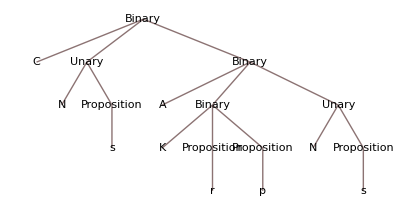

```mathematica
TreeForm@$p@"CNsAKrpNs"
```

Using Jabelean’s solver (in JacquardSolver.m in the preliminary packages section of this document)

```mathematica
KB={
rl[{},$p@"CNsAKrpNs"],
rl[{},$p@"CNCrpKNpAsr"],
rl[{},$p@"CCpsCCsrCpr"],
rl[{},$p@"CsCKpNsANqs"],
rl[{Binary["C",var[l],var[r]],var[l]},var[r]]
};
```

```mathematica
prettifySolutions[solnss_]:=
gridRules@(
(solns↦
(soln↦soln⟦1⟧->$u@soln⟦2⟧)/@
solns)/@
solnss)
```

This next directly answers 2 on page 90.

```mathematica
Solutions[Binary["C",var[x],$p@"AKrpNs"],KB]
```

{{var[x]→Unary[N,Proposition[s]]}}

```mathematica
prettifySolutions@Solutions[Binary["C",var[x],$p@"AKrpNs"],KB]
```

var | x | Ns

It’s not able to dig inside terms looking for an A:

```mathematica
prettifySolutions@Solutions[Binary["A",var[x],var[y]],KB]
```

#### Experiment with Cabrera’s solver

```mathematica
ClearAll[Knowledge,Statements];
SetAttributes[Statements,{Flat,Orderless}]
Knowledge=Statements[
$p@"CNsAKrpNs",
$p@"CNCrpKNpAsr",
$p@"CCpsCCsrCpr",
$p@"CsCKpNsANqs"
];
$u/@Question[Knowledge, Binary["C",X_,$p@"AKrpNs"], X]
```

{Ns}

A limitation of Cabrera’s solver is that it eagerly expands rules into facts, explosively, perhaps even infinitely, consuming memory. Until we make this lazy, we’ll use Jabelean’s solver, which is slower than Cabrera’s because it does not use Mathematica’s pattern matching.

#### Back to Jabelean’s solver

This next shows that the solver is bi-directional:

```mathematica
prettifySolutions@
Solutions[Binary["C",$p@"Ns",var[y]],KB]
```

var | y | AKrpNs

The next two show similar solutions for different L and R terms in a CLR.

```mathematica
prettifySolutions@
Solutions[Binary["C",var[x],$p@"KNpAsr"],KB]
```

var | x | NCrp

```mathematica
prettifySolutions@
Solutions[Binary["C",$p@"NCrp",var[y]],KB]
```

var | y | KNpAsr

#### Example 8 (3 on page 90 of Wff-n-Proof)

Can we find a CLR given an L and an R?

We can find all CLRs in the fact base, then filter them down to the ones that match our given L and R. We’ll do the filtering with a post-processing phase, to the solver. The solver’s job is to give us all CLRs in the fact base.

```mathematica
prettifySolutions@
Solutions[Binary["C",var[x],var[y]],KB]
```

var | x | Cps
var | y | CCsrCpr
var | x | s
var | y | CKpNsANqs
var | x | NCrp
var | y | KNpAsr
var | x | Ns
var | y | AKrpNs

```mathematica
select[L_String,R_String]:=
soln↦
Select[soln,
rules↦
$u@(var[x]/.rules)===L&&
$u@(var[y]/.rules)===R]
```

```mathematica
prettifySolutions@
select["NCrp","KNpAsr"]@Solutions[Binary["C",var[x],var[y]],KB]
```

var | x | NCrp
var | y | KNpAsr

We can also do it much faster and shorter by the direct but “out-of-the-box” pseudo-inference rule CoR:

```mathematica
And[$p@"NCrp",$p@"KNpAsr"]/.CoR//$u
```

CNCrpKNpAsr

#### Page 91 of Wff-n-Proof

The first one is a proper application of the true inference rule Co:

```mathematica
And[$p@"CKNprs",$p@"KNpr"]/.Co//$u
```

s

The second one requires a solution, that is, finding a CLR and L that would imply R

```mathematica
prettifySolutions@
select["Cps","CCsrCpr"]@
Solutions[Binary["C",var[x],var[y]],KB]
```

var | x | Cps
var | y | CCsrCpr

Or writing it all out

```mathematica
(Binary["C",var[x],var[y]]/.
(select["Cps","CCsrCpr"]@
Solutions[Binary["C",var[x],var[y]],KB])⟦1⟧)//
$u
```

CCpsCCsrCpr

We can do the same with the bogus pseudorule CoR

```mathematica
And[
$p@"Cps",
$p@"CCsrCpr"]/.CoR//$u
```

CCpsCCsrCpr

The third one also requires a solution:

```mathematica
prettifySolutions@
Solutions[Binary["C",var[x],$p@"CKpNsANqs"],KB]
```

var | x | s

or an application of the bogus pseudorule CoL

```mathematica
And[
$p@"CsCKpNsANqs",
$p@"CKpNsANqs"]/.CoL//$u
```

s

### Proofs (page 92 ff)

```mathematica
ClearAll[inferStep,writeStep,writeProof];
inferStep[truths_,premise_?AtomQ,rule_]:=(truths⟦premise⟧)/.rule;
inferStep[truths_,premises_,rule_]:=truths⟦#⟧&/@premises/.rule;
SetAttributes[writeStep,HoldAll];
writeStep[truths_,{piPair:{premise_,rule_}}]:=
$u/@Append[truths,inferStep[truths,premise,rule]];
writeStep[truths_,{piPair:{premise_,rule_},morePairs__}]:=
writeStep[Append[truths,inferStep[truths,premise,rule]],{morePairs}];
SetAttributes[writeProof,HoldAll];
writeProof[suppositions_List,pairs_List]:=
writeStep[$p/@suppositions,pairs];
```

#### P1 — page 92

```mathematica
writeProof[{"Cpr","Kpq"},{{2,KoL},{1&&3,Co}}]
```

{Cpr,Kpq,p,r}

#### P2 — page 93

```mathematica
writeProof[{"p","KsCpr"},{{2,KoL},{2,KoR},{4&&1,Co},{3&&5,Ki}}]
```

{p,KsCpr,s,Cpr,r,Ksr}

#### P3 — page 93

```mathematica
writeProof[{"p","Crs","Cpr"},{{3&&1,Co},{2&&4,Co},{1&&5,Ki}}]
```

{p,Crs,Cpr,r,s,Kps}

#### P4 — page 93

```mathematica
writeProof[{"KsCNqNr","Csp","CpNq"},{{1,KoL},{2&&4,Co},{3&&5,Co},{1,KoR},{7&&6,Co}}]
```

{KsCNqNr,Csp,CpNq,s,p,Nq,CNqNr,Nr}

#### P5 — page 93

```mathematica
writeProof[{"Kpq","Cpr","Cqs"},{
{1,KoL},
{2&&4,Co},
{1,KoR},
{3&&6,Co},
{5&&7,Ki}}]
```

{Kpq,Cpr,Cqs,p,r,q,s,Krs}

#### P6 — page 94

```mathematica
writeProof[{"KpCqr","KCsqCps"},{
{1,KoL},
{2,KoR},
{4&&3,Co},
{2,KoL},
{6&&5,Co},
{1,KoR},
{8&&7,Co}}]
```

{KpCqr,KCsqCps,p,Cps,s,Csq,q,Cqr,r}

#### P7 — page 94

```mathematica
writeProof[{"CpKqCsr","KpCqs"},{
{2,KoL},
{1&&3,Co},
{4,KoL},
{2,KoR},
{6&&5,Co},
{4,KoR},
{8&&7,Co}}]
```

{CpKqCsr,KpCqs,p,KqCsr,q,Cqs,s,Csr,r}

#### P8 — page 95

```mathematica
writeProof[{"KpCKpqr","Kqs"},{
{1,KoL},
{2,KoL},
{3&&4,Ki},
{1,KoR},
{6&&5,Co},
{2,KoR},
{7&&8,Ki}}]
```

{KpCKpqr,Kqs,p,q,Kpq,CKpqr,r,s,Krs}

#### P9 — page 95

```mathematica
writeProof[{"CpCqCrs","Kpq","r"},{
{2,KoL},
{1&&4,Co},
{2,KoR},
{5&&6,Co},
{7&&3,Co},
{8&&3,Ki}
}]
```

{CpCqCrs,Kpq,r,p,CqCrs,q,Crs,s,Ksr}

#### P10 — page 95

Now do a little more to make them pretty:

```mathematica
Zip[
Range[10],
writeProof[{"KsCsq","CqCsr"},{
{1,KoL},
{1,KoR},
{4&&3,Co},
{2&&5,Co},
{6&&3,Co}}],
List]//MatrixForm
```

(1 | KsCsq
2 | CqCsr
3 | s
4 | Csq
5 | q
6 | Csr
7 | r)

#### Page 101 — need to modify write-proof to handle symbolic indices

```mathematica
Zip[
Range[10],
writeProof[{"Kqp"},{{1,KoL},{1,KoR},{2&&3,Ki},{1:>4,Ci}}],
List
]//MatrixForm
```

(1 | Kqp
2 | q
3 | p
4 | Kqp
5 | CKqpKqp)

Format a truth as a quadruple of an index, a premise form — a combination of indices, a rule, and an output. A step consists in writing a new truth into the table of truths.

```mathematica
ClearAll[inferStep2,writeStep2,writeProof2];
```

```mathematica
InferenceRuleNames[Supp]="Supp";
inferStep2[truths_,premise_?AtomQ,rule_]:=(truths[premise]⟦4⟧)/.rule;
inferStep2[truths_,premises_,rule_]:=truths[#]⟦4⟧&/@premises/.rule;
SetAttributes[writeStep2,HoldAll];
writeStep2[truths_,{triple:{index_,premise_,rule_,commentary___}}]:=
(truths[index]=Append[triple⟦1;;3⟧(* discard commentary *),inferStep2[truths,premise,rule]];
Module[{d=DownValues[truths]},
{#⟦2,1⟧,$u@#⟦2,4⟧,#⟦2,2⟧,InferenceRuleNames[#⟦2,3⟧]}&/@d//MatrixForm]);
writeStep2[truths_,{triple:{index_,premise_,rule_,commentary___},more__}]:=
(truths[index]=Append[triple⟦1;;3⟧(* discard commentary *),inferStep2[truths,premise,rule]];
writeStep2[truths,{more}]);
SetAttributes[writeProof2,HoldAll];
writeProof2[supps_List,triples_List]:=
Module[{truths},
Map[
s↦truths[s⟦1⟧]={s⟦1⟧,s⟦1⟧,Supp,$p@s⟦2⟧},supps];
writeStep2[truths,triples]];
```

#### P1 — page 101, written prettily

```mathematica
writeProof2[{{"1a","Kqp"}},{
{"1b","1a",KoL},
{"1c","1a",KoR},
{"1d","1c"&&"1b",Ki},
{"2","1a":>"1d",Ci}}]
```

(1a | Kqp | 1a | Supp
1b | q | 1a | KoL
1c | p | 1a | KoR
1d | Kpq | 1c&&1b | Ki
2 | CKqpKpq | 1a:>1d | Ci)

#### P8 — page 95, even prettier

```mathematica
writeProof2[{{1,"KpCKpqr"},{2,"Kqs"}},{
{3,1,KoL},
{4,2,KoL},
{5,3&&4,Ki},
{6,1,KoR},
{7,6&&5,Co},
{8,2,KoR},
{9,7&&8,Ki}}]
```

(1 | KpCKpqr | 1 | Supp
2 | Kqs | 2 | Supp
3 | p | 1 | KoL
4 | q | 2 | KoL
5 | Kpq | 3&&4 | Ki
6 | CKpqr | 1 | KoR
7 | r | 6&&5 | Co
8 | s | 2 | KoR
9 | Krs | 7&&8 | Ki)

#### P9 — page 95, even prettier

```mathematica
writeProof2[{{1,"CpCqCrs"},{2,"Kpq"},{3,"r"}},{
{4,2,KoL},
{5,1&&4,Co},
{6,2,KoR},
{7,5&&6,Co},
{8,7&&3,Co},
{9,8&&3,Ki}
}]
```

(1 | CpCqCrs | 1 | Supp
2 | Kpq | 2 | Supp
3 | r | 3 | Supp
4 | p | 2 | KoL
5 | CqCrs | 1&&4 | Co
6 | q | 2 | KoR
7 | Crs | 5&&6 | Co
8 | s | 7&&3 | Co
9 | Ksr | 8&&3 | Ki)

#### P10 — page 95, even prettier

```mathematica
writeProof2[{{1,"KsCsq"},{2,"CqCsr"}},{
{3,1,KoL},
{4,1,KoR},
{5,4&&3,Co},
{6,2&&5,Co},
{7,6&&3,Co}}]
```

(1 | KsCsq | 1 | Supp
2 | CqCsr | 2 | Supp
3 | s | 1 | KoL
4 | Csq | 1 | KoR
5 | q | 4&&3 | Co
6 | Csr | 2&&5 | Co
7 | r | 6&&3 | Co)

### Deeper Deductions

#### P2 — page 103

```mathematica
writeProof2[{{"1a","q"},{"1b1","KrCrs"}},{
{"1b2","1b1",KoL},
{"1b3","1b1",KoR},
{"1b4","1b3"&&"1b2",Co},
{"1c","1b1":>"1b4",Ci},
{"2","1a":>"1c",Ci}
}]
```

(1a | q | 1a | Supp
1b1 | KrCrs | 1b1 | Supp
1b2 | r | 1b1 | KoL
1b3 | Crs | 1b1 | KoR
1b4 | s | 1b3&&1b2 | Co
1c | CKrCrss | 1b1:>1b4 | Ci
2 | CqCKrCrss | 1a:>1c | Ci)

#### P3 — page 110

```mathematica
writeProof2[{
{"1a","Krs"}
},{
{"1b","1a",KoL},
{"1c","1a",KoL},
{"1d","1a",KoR},
{"1e","1b"&&"1c",Ki},
{"1f","1d"&&"1e",Ki},
{"2","1a":>"1f",Ci}
}]
```

(1a | Krs | 1a | Supp
1b | r | 1a | KoL
1c | r | 1a | KoL
1d | s | 1a | KoR
1e | Krr | 1b&&1c | Ki
1f | KsKrr | 1d&&1e | Ki
2 | CKrsKsKrr | 1a:>1f | Ci)

#### P4 — page 112

```mathematica
writeProof2[{
{"1a","KpCpq"}
},{
{"1b","1a",KoL},
{"1c","1a",KoR},
{"1d","1c"&&"1b",Co},
{"2","1a":>"1d",Ci}
}]
```

(1a | KpCpq | 1a | Supp
1b | p | 1a | KoL
1c | Cpq | 1a | KoR
1d | q | 1c&&1b | Co
2 | CKpCpqq | 1a:>1d | Ci)

Proper use of the Ci-practice form would require us to parse the names of the inferences in the first columns of the displays. All the items marked 1a through 1d in P4 above, for example, constitute a lemma (called a sub-proof in the game manual). Proper use of Ci in the game is to cite the lemma as justification, rather than to cite individual lines in it. For instance, in line 2 of P4 above, we should say “1” instead of “1a:>1d”. To implement such in our game would require introducing substructure into the naming of lines of inference. (UNDONE).

The following example illustrates even one more level of sub-structure.

Add another slot on each inference line for commentary.

#### P5 — page 114

```mathematica
writeProof2[{
{"1a","q"},
{"1b1","Krp"}
},{
{"1b2","1b1",KoR,"p"},
{"1c","1b1":>"1b2",Ci,"CKrpp"},
{"2","1a":>"1c",Ci,"CqCKrpp"}
}]
```

(1a | q | 1a | Supp
1b1 | Krp | 1b1 | Supp
1b2 | p | 1b1 | KoR
1c | CKrpp | 1b1:>1b2 | Ci
2 | CqCKrpp | 1a:>1c | Ci)

#### P6 — page 114

```mathematica
writeProof2[{
{"1a","KsCsr"}
},{
{"1b","1a",KoL,"s"},
{"1c","1a",KoR,"Csr"},
{"1d","1c"&&"1b",Co,"r"},
{"1e","1d"&&"1b",Ki,"Krs"},
{"1f","1b"&&"1e",Ki,"KsKrs"},
{"2","1a":>"1f",Ci,"CKsCsrKsKrs"}
}]
```

(1a | KsCsr | 1a | Supp
1b | s | 1a | KoL
1c | Csr | 1a | KoR
1d | r | 1c&&1b | Co
1e | Krs | 1d&&1b | Ki
1f | KsKrs | 1b&&1e | Ki
2 | CKsCsrKsKrs | 1a:>1f | Ci)

#### P7 — page 116 —> CCCKpqprr

```mathematica
writeProof2[{
{"1a","CCKpqpr"},
{"1b1","Kpq"}
},{
{"1b2","1b1",KoL,"p"},
{"1c","1b1":>"1b2",Ci,"CKpqp"},
{"1d","1a"&&"1c",Co,"r"},
{"2","1a":>"1d",Ci,"CCCKpqprr"}
}]
```

(1a | CCKpqpr | 1a | Supp
1b1 | Kpq | 1b1 | Supp
1b2 | p | 1b1 | KoL
1c | CKpqp | 1b1:>1b2 | Ci
1d | r | 1a&&1c | Co
2 | CCCKpqprr | 1a:>1d | Ci)

#### P8 — page 116 —> CApqCNpCKrsr

The pattern emerging is that every time I see a C, I am going to nest a level in my proof structure. The new level is a lemma that assumes the premise and tries independently to prove the consequent of the C.

```mathematica
writeProof2[{
{"1a","Apq"},
{"1b1","Np"},
{"1b2a","Ksr"}
},{
{"1b2b","1b2a",KoR,"r"},
{"1b3","1b2a":>"1b2b",Ci,"CNpCKrsr"},
{"1c","1b1":>"1b3",Ci,"CnpCKrsr"},
{"2","1a":>"1c",Ci,"CApqCNpCKrsr"}
}]
```

(1a | Apq | 1a | Supp
1b1 | Np | 1b1 | Supp
1b2a | Ksr | 1b2a | Supp
1b2b | r | 1b2a | KoR
1b3 | CKsrr | 1b2a:>1b2b | Ci
1c | CNpCKsrr | 1b1:>1b3 | Ci
2 | CApqCNpCKsrr | 1a:>1c | Ci)

#### P9 — page 116 —> CNsCNpCsCKrCrqq

```mathematica
writeProof2[{
{"1a","Ns"},
{"1b1","Np"},
{"1b2a","s"},
{"1b2b1","KrCrq"}
},{
{"1b2b2","1b2b1",KoL,"r"},
{"1b2b3","1b2b1",KoR,"Crq"},
{"1b2b4","1b2b2"&&"1b2b3",Co,"q"},
{"1b2c","1b2b1":>"1b2b4",Ci,"CKrCrqq — lemma"},
{"1b3","1b2a":>"1b2c",Ci,"CsCKrCrqq — lemma"},
{"1c","1b1":>"1b3",Ci,"CNpCsCKrCrqq — lemma"},
{"2","1a":>"1c",Ci}
}]
```

(1a | Ns | 1a | Supp
1b1 | Np | 1b1 | Supp
1b2a | s | 1b2a | Supp
1b2b1 | KrCrq | 1b2b1 | Supp
1b2b2 | r | 1b2b1 | KoL
1b2b3 | Crq | 1b2b1 | KoR
1b2b4 | q | 1b2b2&&1b2b3 | Co
1b2c | CKrCrqq | 1b2b1:>1b2b4 | Ci
1b3 | CsCKrCrqq | 1b2a:>1b2c | Ci
1c | CNpCsCKrCrqq | 1b1:>1b3 | Ci
2 | CNsCNpCsCKrCrqq | 1a:>1c | Ci)

#### P10 — page 117 —> CpCqCNqCNpCKCrsrs

At this point, I am using the proof machinery as fancy pencil-and-paper layout. It’s not actually doing any checking, structuring, or destructuring for me, just straight lookup and substitution. I’m doing the proofs; it’s just writing them out for me in a pretty format.

Rhetorically, this is an interesting case. We pose conditionals that alternately presume q and Nq, p and Np and derive a true statement that if some final conditional, Crs, and its premise, r, then then its consequent, s. A listener to a real argument structured this way might hear that some contradiction resulted in an independent truth. But, there is no contradiction because everything was conditional and the final result, CKCrsrs, did not depend on p and q, the alternating premises.

```mathematica
writeProof2[{
{"1a","p"},
{"1b1","q"},
{"1b2a","Nq"},
{"1b2b1","Np"},
{"1b2b2a","KCrsr"}
},{
{"1b2b2b","1b2b2a",KoR,"r"},
{"1b2b2c","1b2b2a",KoL,"Crs"},
{"1b2b2d","1b2b2b"&&"1b2b2c",Co,"s"},
{"1b2b3","1b2b2a":>"1b2b2d",Ci,"CKCrsrs"},
{"1b2c","1b2b1":>"1b2b3",Ci,"CNpCKCrsrs"},
{"1b3","1b2a":>"1b2c",Ci,"CNqCNpCKCrsrs"},
{"1c","1b1":>"1b3",Ci,"CqCNqCNpCKCrsrs"},
{"2","1a":>"1c",Ci,"CpCqCNqCNpCKCrsrs"}
}]
```

(1a | p | 1a | Supp
1b1 | q | 1b1 | Supp
1b2a | Nq | 1b2a | Supp
1b2b1 | Np | 1b2b1 | Supp
1b2b2a | KCrsr | 1b2b2a | Supp
1b2b2b | r | 1b2b2a | KoR
1b2b2c | Crs | 1b2b2a | KoL
1b2b2d | s | 1b2b2b&&1b2b2c | Co
1b2b3 | CKCrsrs | 1b2b2a:>1b2b2d | Ci
1b2c | CNpCKCrsrs | 1b2b1:>1b2b3 | Ci
1b3 | CNqCNpCKCrsrs | 1b2a:>1b2c | Ci
1c | CqCNqCNpCKCrsrs | 1b1:>1b3 | Ci
2 | CpCqCNqCNpCKCrsrs | 1a:>1c | Ci)

### Reiteration — page 119ff

```mathematica
DefineInferenceRule[R,left_:>left];
```

```mathematica
writeProof2[{
{"1","CKpqr"},
{"2a","p"},
{"2c1","q"}
},{
{"2b","1",R,"CKpqr"},
{"2c2","2a",R,"p"}
}]
```

(1 | CKpqr | 1 | Supp
2a | p | 2a | Supp
2b | CKpqr | 1 | R
2c1 | q | 2c1 | Supp
2c2 | p | 2a | R)

Do a better job of laying out proofs; page 122ff

```mathematica
{{"1", "CKpqr", "s"}, {"2", □, □}}
```

{{1,CKpqr,s},{2,□,□}}

```mathematica
%//FullForm
```

List[List["1","CKpqr","s"],List["2",\[Placeholder],\[Placeholder]]]

```mathematica
%%
```

{{1,CKpqr,s},{2,□,□}}

```mathematica
{{"1","CKpqr","s"},{"2",□,□}}
```

{{1,CKpqr,s},{2,□,□}}

Here’s an approach to the sequences, but it creates difficulties for the justifications.

```mathematica
Grid[{
(*{"P1","CKpqr -> CpCqr"},*)
{Grid[{
{"1","CKpqr"},
{"2",Grid[{
{"a","p"},
{"b","CKpqr"},
{"c",Grid[{
{"1","q"},
{"2","p"},
{"3","Kpq"},
{"4","CKpqr"},
{"5","r"}
},Frame->All]},
{"d","Cqr"}
},Frame->All]},
{"3","CpCqr"}
},Frame->All]}
},Frame->All]
```

1 | CKpqr
2 | a | p
b | CKpqr
c | 1 | q
2 | p
3 | Kpq
4 | CKpqr
5 | r
d | Cqr
3 | CpCqr

Suppose we know at the outset how many levels of nesting we need. we can then use SpanFromLeft to leave judicious spacing.

```mathematica
sl=SpanFromLeft
```

```mathematica
{{"1", "CKpqr", sl, sl, "s"}, {"2", "a", "p", sl, "s"}, {sl, "b", "CKqpr", sl, "1,R"}, {sl, "c", "1", "q", "s"}, {sl, sl, "2", "p", "a,R"}, {sl, sl, "3", "Kpq", "2,1,Ki"}, {sl, sl, "4", "CKpqr", "b,R"}, {sl, sl, "5", "r", "4,3,Co"}, {sl, "d", "Cqr", sl, "c,Ci"}, {"3", "CpCqr", sl, sl, "2,Ci"}}//Grid[#,Frame->All]&
```

1 | CKpqr |  |  | s
2 | a | p |  | s
 | b | CKqpr |  | 1,R
 | c | 1 | q | s
 |  | 2 | p | a,R
 |  | 3 | Kpq | 2,1,Ki
 |  | 4 | CKpqr | b,R
 |  | 5 | r | 4,3,Co
 | d | Cqr |  | c,Ci
3 | CpCqr |  |  | 2,Ci

```mathematica
{{"1", sl, sl, "CKpqr", "s"}, {"2", "a", sl, "p", "s"}, {"", "b", sl, "CKqpr", "1,R"}, {"", "c", "1", "q", "s"}, {"", "", "2", "p", "a,R"}, {"", "", "3", "Kpq", "2,1,Ki"}, {"", "", "4", "CKpqr", "b,R"}, {"", "", "5", "r", "4,3,Co"}, {"", "d", sl, "Cqr", "c,Ci"}, {"3", sl, sl, "CpCqr", "2,Ci"}}//Grid[#,Frame->All,Alignment->Left]&
```

1 |  |  | CKpqr | s
2 | a |  | p | s
 | b |  | CKqpr | 1,R
 | c | 1 | q | s
 |  | 2 | p | a,R
 |  | 3 | Kpq | 2,1,Ki
 |  | 4 | CKpqr | b,R
 |  | 5 | r | 4,3,Co
 | d |  | Cqr | c,Ci
3 |  |  | CpCqr | 2,Ci

```mathematica
{{"1", sl, sl, "CKpqr", "s"}, {"2", "a", sl, "p", "s"}, {"2", "b", sl, "CKqpr", "1,R"}, {"2", "c", "1", "q", "s"}, {"2", "c", "2", "p", "a,R"}, {"2", "c", "3", "Kpq", "2,1,Ki"}, {"2", "c", "4", "CKpqr", "b,R"}, {"2", "c", "5", "r", "4,3,Co"}, {"2", "d", sl, "Cqr", "c,Ci"}, {"3", sl, sl, "CpCqr", "2,Ci"}}//Grid[#,Frame->All,Alignment->Left]&
```

1 |  |  | CKpqr | s
2 | a |  | p | s
2 | b |  | CKqpr | 1,R
2 | c | 1 | q | s
2 | c | 2 | p | a,R
2 | c | 3 | Kpq | 2,1,Ki
2 | c | 4 | CKpqr | b,R
2 | c | 5 | r | 4,3,Co
2 | d |  | Cqr | c,Ci
3 |  |  | CpCqr | 2,Ci

```mathematica
{{"1", , , "CKpqr", "s"}, {"2", "a", , "p", "s"}, {"2", "b", , "CKqpr", "1,R"}, {"2", "c", "1", "q", "s"}, {"2", "c", "2", "p", "a,R"}, {"2", "c", "3", "Kpq", "2,1,Ki"}, {"2", "c", "4", "CKpqr", "b,R"}, {"2", "c", "5", "r", "4,3,Co"}, {"2", "d", , "Cqr", "c,Ci"}, {"3", , , "CpCqr", "2,Ci"}}//Grid[#,Frame->All,Alignment->Left]&
```

1 |  |  | CKpqr | s
2 | a |  | p | s
2 | b |  | CKqpr | 1,R
2 | c | 1 | q | s
2 | c | 2 | p | a,R
2 | c | 3 | Kpq | 2,1,Ki
2 | c | 4 | CKpqr | b,R
2 | c | 5 | r | 4,3,Co
2 | d |  | Cqr | c,Ci
3 |  |  | CpCqr | 2,Ci

```mathematica
{{"1", , , "CKpqr", "s"}, {"2", "a", , "p", "s"}, {"", "b", , "CKqpr", "1,R"}, {"", "c", "1", "q", "s"}, {"", "", "2", "p", "a,R"}, {"", "", "3", "Kpq", "2,1,Ki"}, {"", "", "4", "CKpqr", "b,R"}, {"", "", "5", "r", "4,3,Co"}, {"", "d", , "Cqr", "c,Ci"}, {"3", , , "CpCqr", "2,Ci"}}//Grid[#,Frame->All,Alignment->Left]&
```

1 |  |  | CKpqr | s
2 | a |  | p | s
 | b |  | CKqpr | 1,R
 | c | 1 | q | s
 |  | 2 | p | a,R
 |  | 3 | Kpq | 2,1,Ki
 |  | 4 | CKpqr | b,R
 |  | 5 | r | 4,3,Co
 | d |  | Cqr | c,Ci
3 |  |  | CpCqr | 2,Ci

```mathematica
sa=SpanFromAbove;sb=SpanFromBoth;
```

```mathematica
{{"P1", sl, sl, "CpCqr", "CKpqr"}, {sa, sb, sb, sa, sa}, {"1", sl, sl, "CKpqr", "s"}, {"2", "a", sl, "p", "s"}, {"", "b", sl, "CKqpr", "1,R"}, {"", "c", "1", "q", "s"}, {"", "", "2", "p", "a,R"}, {"", "", "3", "Kpq", "2,1,Ki"}, {"", "", "4", "CKpqr", "b,R"}, {"", "", "5", "r", "4,3,Co"}, {"", "d", sl, "Cqr", "c,Ci"}, {"3", sl, sl, "CpCqr", "2,Ci"}}//Grid[#,Frame->All,Alignment->Left]&
```

P1 |  |  | CpCqr | CKpqr
 |  |  |  | 
1 |  |  | CKpqr | s
2 | a |  | p | s
 | b |  | CKqpr | 1,R
 | c | 1 | q | s
 |  | 2 | p | a,R
 |  | 3 | Kpq | 2,1,Ki
 |  | 4 | CKpqr | b,R
 |  | 5 | r | 4,3,Co
 | d |  | Cqr | c,Ci
3 |  |  | CpCqr | 2,Ci

There’s the pattern I like best. How to get that from a sequence of proofs and sub-proofs?

Perhaps automating the layout is overkill. Let’s focus on filling in the content.

The numbers / letters / keys for application of rule R refer to one level out. The keys for application of other rules refer to the current level.

## ALGEBRA-1 EXPRESSIONS

```mathematica
ClearAll[F]; (* for "Field" *)
F[Expr]=({{FSum}, {FProd}, {FVar}, {FInt}});(* "Sum" collides with a built-in. *)
F[FSum]={{Plus,Expr,Expr}}; (* Do we want the built-in "Plus"? *)
F[FInt]={{RandomInteger}};
F[FVar]={
(*{a},{b},{c},{d},{e},{f},{g},{h},{i},{j},{k},{m},{n},*)
{x},{y},{z},{-x},{-y},{-z},{1/x},{1/y},{1/z}
(*,{u},{v},{w},{p},{q},{r},{s},{t}*)};
F[FProd]={{Times,Expr,Expr}};
F[Start]={{Expr}};
```

```mathematica
visGrammar@F
```

visGrammar[F]

```mathematica
(FProbabilized=injectGenerationProbabilities[F,
Function[list,
If[list==={{FSum},{FProd}},{.5,.5},
equiProbabilities@list]]
])//visGrammar
```

visGrammar[newTable$19519]

```mathematica
ClearAll[$exprTable];
parserPatterns[F,$exprTable];
```

```mathematica
SeedRandom[42];
With[{gengen=
((generateSentence[FProbabilized,FVar,terminalsFromGrammar@F,10]//InputForm))&},
DynamicModule[{foo=gengen[]},
Manipulate[foo,Button["GEN",foo=gengen[]]]]]
```

```mathematica
ClearAll[$fexpr];
$fexpr[dummy_,depth_:20]:=
With[{sen=generateSentence[
FProbabilized,FVar,terminalsFromGrammar@F,depth]},
With[{parse=($exprTable@sen)[[2]]},
With[{interp={
FInt[RandomInteger]:>RandomInteger[10],
FVar->Identity,
(FSum|FProd)[f_,args__]:>Apply[f,{args}]}},
{TreeForm[parse,VertexLabeling->Automatic],(parse//.interp//FullSimplify)}]]]
```

```mathematica
$fcontender=0;
Animate[
Module[{t,e},
{t,e}=$fexpr[dummy];
With[{le=LeafCount[e]},
If[le>LeafCount@$fcontender,$fcontender=e];
Grid[{{e,SpanFromLeft},{le,t}},Frame->All]]],
{dummy,1,25,1}]
```

Biggest one found so far:

```mathematica
Dynamic[$fcontender]
```

## DEEPER EXAMPLE: BENPIERCE TYPES

Encode types from Benjamin C. Pierce’s book, TPL or “Types and Programming Languages.”

Call the grammar “BPT,” for “Ben Pierce Terms,” from Section 3.1 of his book. It has ONE non-terminal symbol. He calls it “t.” That’s too small for us. We’ll call it “Term.”

## UNTYPED UTTERANCES

Consistent with Sections 3.2 and 4.1 of TPL.

BP’s Ternary if foo then bar else baz is not in Polish prefix form. Prefix form would be if foo bar baz, much easier to parse with our nearly-trivial tools. Go there, because the point of this exercise is not to spend time on parsing, but to spend time on types.

```mathematica
ClearAll[BPT,Term,Ternary,Unary,BPTtokens];
BPT[Term]=({{Const}, {Ternary}, {Unary}});
BPT[Const]=({{"true"}, {"false"}, {"0"}}); (* groundTerm for travesties *)
(* incovenient to parse with present tools *)
(*BPT[Ternary]={{"if",Term,"then",Term,"else",Term}};*)
BPT[Ternary]={{"if", Term, Term,Term}};
BPT[Unary]=({{"succ", Term}, {"pred", Term}, {"iszero", Term}});
BPT[Start]={{Term}};
```

from Section 4.1:

```mathematica
ClearAll[isnumerical];
isnumerical[Const["0"]]:=True;
isnumerical[Unary["succ",t1_]]:=isnumerical@t1;
isnumerical[_]:=False;

ClearAll[isval];
isval[Const["true"]]:=True;
isval[Const["false"]]:=True;
isval[t_?isnumerical]:=True;

isval[Const["0"]]
```

True

```mathematica
ClearAll[visGrammar];
visGrammar[g_]:=Module[{d=DownValues[g]},
Zip[
Function[hp,hp[[1,1,1]]]/@Unevaluated/@d,
Function[hp,hp[[1,1]]]/@d,Rule]]//gridRules;
visGrammar[BPT]
```

Const | true
false
0
Start | Term
Term | Const
Ternary
Unary
Ternary | if
Term
Term
Term
Unary | succ
Term
pred
Term
iszero
Term

```mathematica
allSymbols@BPT//gridExpression
```

| 0
 | false
 | if
 | iszero
 | pred
List | succ
 | true
 | Const
 | Term
 | Ternary
 | Unary

```mathematica
ClearAll[$bptTable];
parserPatterns[BPT,$bptTable];
DownValues@$bptTable//TableForm
```

HoldPattern[$bptTable[{tok$20669:true|false|0,toks$20669___},tree$20669_:Null]]:>genParserBody[0,tok$20669,{toks$20669},Const,{},$bptTable]
HoldPattern[$bptTable[{},tree_:Null]]:>{{},tree}
HoldPattern[$bptTable[{tok$20673:Alternatives[if],toks$20673___},tree$20673_:Null]]:>genParserBody[3,tok$20673,{toks$20673},Ternary,{},$bptTable]
HoldPattern[$bptTable[{tok$20675:succ|pred|iszero,toks$20675___},tree$20675_:Null]]:>genParserBody[1,tok$20675,{toks$20675},Unary,{},$bptTable]
HoldPattern[$bptTable[xs$___]]:>Throw[{ToString[$bptTable]<>: CATASTROPHE: ,xs$}]

Generate some travesties from this grammar, BPT. Equiprobabilities doesn’t generate enough variety, so we’ll build a probability-assignment function up by hand.

```mathematica
??equiProbabilities
```

```mathematica
ClearAll[BPTprobabilities];
BPTprobabilities[list_List]:=If[list==={{Const},{Ternary},{Unary}},
{.25,.50,.25}, equiProbabilities@list];
```

```mathematica
(BPTprobabilized=injectGenerationProbabilities[BPT,BPTprobabilities])//visGrammar
```

Const | probability | 0.333333
alternative | true
probability | 0.333333
alternative | false
probability | 0.333333
alternative | 0
Start | probability | 1.
alternative | Term
Term | probability | 0.25
alternative | Const
probability | 0.5
alternative | Ternary
probability | 0.25
alternative | Unary
Ternary | probability | 1.
alternative | if
Term
Term
Term
Unary | probability | 0.333333
alternative | succ
Term
probability | 0.333333
alternative | pred
Term
probability | 0.333333
alternative | iszero
Term

```mathematica
ClearAll[spaceRules];
spaceRules={x_String:>x<>" "};
```

```mathematica
SeedRandom[26];
expressionStringFromSentence[generateSentence[BPTprobabilized,Const,terminalsFromGrammar@BPT,10],spaceRules]
```

pred iszero if 0 0 0

The parser, itself, is a composition of partTree (‘cadr’), the parser table above, and a tokenizer function, which will just be StringSplit for this application:

```mathematica
SeedRandom[26];
DynamicModule[{foo=generateSentence[BPTprobabilized,Const,terminalsFromGrammar@BPT,20]},
Manipulate[foo,
Button["GEN",foo=generateSentence[BPTprobabilized,Const,terminalsFromGrammar@BPT,20]]]]
```

In the display below, hover over a vertex to see its content.

```mathematica
SeedRandom[26];
With[{gengen=Module[{},
With[{sen=generateSentence[BPTprobabilized,Const,terminalsFromGrammar@BPT,20]},
With[{tpt=Timing@$bptTable@sen},
Column[{sen,
ToString[Length@sen]<>" Leaves",
ToString@tpt[[1]]*Seconds,
TreeForm[tpt[[2,2]](*,VertexLabeling->Automatic*),ImageSize->Large]},
Frame->All]]]]&},
DynamicModule[{foo=gengen[]},
Manipulate[{foo},
Button["GEN",foo=gengen[]]]]]
```

## SIZE AND DEPTH

## SMALL-STEP OPERATIONAL SEMANTICS

Gin up a sample.

```mathematica
SeedRandom[26];
ClearAll[$test];
($test=$bptTable[generateSentence[BPTprobabilized,Const,terminalsFromGrammar@BPT,20]][[2]])//InputForm
```

Unary["pred", Unary["iszero", Ternary["if", Unary["iszero", 
    Unary["pred", Ternary["if", Const["false"], Const["false"], Const["true"]]]], 
   Unary["iszero", Ternary["if", Ternary["if", Const["false"], Const["false"], 
      Const["false"]], Const["false"], Const["0"]]], 
   Ternary["if", Ternary["if", Const["0"], Ternary["if", Const["0"], Const["0"], 
      Const["0"]], Const["0"]], Unary["iszero", Ternary["if", Const["true"], 
      Const["0"], Const["false"]]], Ternary["if", Unary["succ", Const["0"]], 
     Ternary["if", Const["0"], Const["0"], Const["false"]], 
     Ternary["if", Const["true"], Const["0"], Const["false"]]]]]]]

### Boolean Evaluation Rules

```mathematica
ClearAll[Ternary,evBoolRules35];
(* model E-If with a function representing the premise transition that is above the line. The function returns the transition rules. *)
evBoolRules35[c1_,c1p_]:={
Ternary["if",Const["true"],t1_,t2_]:>t1,
Ternary["if",Const["false"],t1_,t2_]:>t2,
Ternary["if",c1,t1_,t2_]:>Ternary["if",c1p,t1,t2]};
(*Ternary["if",Const["true"],t1_,t2_]:=t1;
Ternary["if",Const["false"],t1_,t2_]:=t2;*)
ClearAll[dpyRules];
dpyRules={Const["0"]->"0",Const["true"]->"#t",Const["false"]->"#f"};
```

```mathematica
$test//.evBoolRules35[Null,Null]/.dpyRules
```

Unary[pred,Unary[iszero,Ternary[if,Unary[iszero,Unary[pred,#t]],Unary[iszero,0],Ternary[if,Ternary[if,0,Ternary[if,0,0,0],0],Unary[iszero,0],Ternary[if,Unary[succ,0],Ternary[if,0,0,#f],0]]]]]

```mathematica
Unary["pred",Unary["iszero",Ternary["if",Unary["iszero",Unary["pred","#t"]],Unary["iszero","0"],Ternary["if",Ternary["if","0",Ternary["if","0","0","0"],"0"],Unary["iszero","0"],Ternary["if",Unary["succ","0"],Ternary["if","0","0","#f"],"0"]]]]]
```

Unary[pred,Unary[iszero,Ternary[if,Unary[iszero,Unary[pred,#t]],Unary[iszero,0],Ternary[if,Ternary[if,0,Ternary[if,0,0,0],0],Unary[iszero,0],Ternary[if,Unary[succ,0],Ternary[if,0,0,#f],0]]]]]

```mathematica
Ternary["if",c1,t1,t2]//.evBoolRules35[c1,c1p]
```

Ternary[if,c1p,t1,t2]

The function for boolRules can be called with complicated arguments:.18

```mathematica
Ternary["if",Ternary["if",Const["true"],Const["false"],Const["true"]],t1,t2]//.evBoolRules35[Ternary["if",Const["true"],Const["false"],Const["true"]],c1p]
```

Ternary[if,c1p,t1,t2]

The following is the derivation tree of Section 3.5.3 in an manually prettified input form. But the output is clear.

```mathematica
Module[{s,t,u,if,$t,$f,rlz},
$t=Const["true"];$f=Const["false"];
if[a_,b_,c_]:=Ternary["if",a,b,c];
s=if[$t,$f,$f];
t=if[s,$t,$t];
u=if[$f,$t,$t];
rlz=evBoolRules35[t,u];
<|"s→false"->(
(s/.rlz)===$f),
"t→u"->
((t/.rlz)===u),
"(if t...)→(if u...)"->
((if[t,$f,$f]/.rlz)===if[u,$f,$f])
|>]
```

<|s→false→True,t→u→True,(if t...)→(if u...)→True|>

### Numerical Evaluation Rules

```mathematica
ClearAll[NB];
NB[Nv]=({{Zero}, {Succ}});
NB[Zero]={{"0"}};
NB[Succ]={{"succ",Nv}};
NB[Start]={{Nv}};
visGrammar[NB];
NBprobabilized=injectGenerationProbabilities[NB,equiProbabilities];
NBprobabilized//visGrammar;
generateSentence[NBprobabilized,Zero,terminalsFromGrammar@NB,20]
ClearAll[$nbTable];
parserPatterns[NB,$nbTable];
DownValues@$nbTable//TableForm;
```

{0}

Some travesties on NB

```mathematica
SeedRandom[26];
With[{gengen=($nbTable@generateSentence[NBprobabilized,Zero,terminalsFromGrammar@NB,40])[[2]]&},
DynamicModule[{foo=gengen[]},
Manipulate[foo,
Button["GEN",foo=gengen[]]]]]
```

??? Cross the syntactic domain of BPT[Term] into the syntactic domain of NB[Nv].

```mathematica
ClearAll[evNumRules35];
evNumRules35[t1_,t1p_]:={
(*Const["0"]->Zero["0"],*)
Unary["pred",Const["0"]]:>Const["0"],
Unary["pred",Unary["succ",nv_]]:>nv,
Unary["iszero",Unary["succ",Const["succ"]]]:>Const["false"],
Unary["succ",t1]:>Unary["succ",t1p],
Unary["pred",t1]:>Unary["pred",t1p],
Unary["iszero",t1]:>Unary["iszero",t1p]
};
```

Above exercise 3.5.14:

```mathematica
Module[{rlz=evNumRules35[Null,Null],p,s,z,znv},
p[nv_]:=Unary["pred",nv];
z=Const["0"];
znv=Zero["0"];
s[nv_]:=Unary["succ",nv];
<|"p 0 → 0"->(p[z]/.rlz)==znv,
"s p 0 → s 0"->(s[p[z]]/.rlz)==s[z],
"p s p 0 → p s 0"->(p@s@p@z//.rlz)==(p@s@z/.rlz)|>]
```

<|p 0 → 0→Const[0]==Zero[0],s p 0 → s 0→True,p s p 0 → p s 0→True|>